```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
```

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[sprtr,ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
sprtr="."
ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

.

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"../msh"}]
```

/home/qzmfrank/codes/rte2dvis/notebook/../msh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

{True,True}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

{True,True}

Thread::tdlen: Objects of unequal length in {{1., 0.}, {1., 1.}, {0., 1.}, {0., 0.}, {0., 0.666667}, {0., 0.333333}, « 9 », {0.5, 0.25392}, {0.24232, 0.75768}, {0.75768, 0.24232}, {0.24232, 0.24232}, {0.75768, 0.75768}} + {{-1., 0.}, « 3 », {« 1 »}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{14, 16, 13}, {14, 13, 15}, {10, 13, 9}, {6, 14, 5}, {8, 16, 7}, {12, 15, 11}, {12, 3, 17}, {8, 1, 18}, {1, 9, 18}, {5, 17, 3}, {6, 4, 19}, {2, 20, 10}, {7, 19, 4}, {2, 11, 20}, {6, 19, 14}, {10, 20, 13}, {13, 18, 9}, {5, 14, 17}, {16, 14, 19}, {13, 20, 15}, {14, 15, 17}, {16, 18, 13}, {16, 8, 18}, {12, 17, 15}, {16, 19, 7}, {11, 15, 20}} + {{-4, -1, -5}, {-2, -3, -5}, {-2, -5, -1}, {-4, -5, -3}} cannot be combined.

Total::normal: Nonatomic expression expected at position 1 in Total[5.40381].

{Total[5.40381],√Root[-5693892816+19239540 #1-14231 #1^2+#1^3&,3]+√Root[-8640+3264 #1-160 #1^2+#1^3&,3]}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
(*
mus[{x_,y_}]:=2x^2+y+Exp[-0.1x-0.2y]
mua[{x_,y_}]:=x+3y^2-Exp[-0.5x+y^2]
*)
mus[{x_,y_}]:=2Log[2]
mua[{x_,y_}]:=Log[2]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi]))(*,CompilationTarget:>"C"*)];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=50;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,SignedAreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
RcPreCalc[pt_]:=With[{a=Norm[#⟦1⟧-#⟦2⟧];b=Norm[#⟦1⟧-#⟦2⟧];c=Norm[#⟦1⟧-#⟦2⟧];},s=0.5(a+b+c);(a b c)/Sqrt[s(s-a)(s-b)(s-c)]]&/@pt
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
r2rFPreCalc[r2rPhi_,phis_]:=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];
SignedAreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Times[#,0.5]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,TRc,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rF=(r2rF=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];)//AbsoluteTiming//#⟦1⟧&;
TsignedArea=(signedArea=SignedAreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=Abs[signedArea];)//AbsoluteTiming//#⟦1⟧&;
TRc=(Rc=Module[{a,b,c,s},
a=Norm[#⟦1⟧-#⟦2⟧];
b=Norm[#⟦2⟧-#⟦3⟧];
c=Norm[#⟦3⟧-#⟦1⟧];
s=0.5(a+b+c);
(a b c)/Sqrt[s(s-a)(s-b)(s-c)]
]&/@pt//Times[#,0.25]&;)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}];

ClearAll[V,VRe,VIm,VElemtRe,VElemtIm,TVRe,TVIm]
VElemtRe=area⟦#⟦1⟧⟧Cos[#⟦2⟧phis]&;
VElemtIm=area⟦#⟦1⟧⟧Sin[#⟦2⟧phis]&;
VElemt=area⟦#⟦1⟧⟧Exp[-ⅈ#⟦2⟧phis]&;
TVRe=(VRe=1.0*VElemtRe[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TVIm=(VIm=1.0*VElemtIm[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
V=1.0*VRe-1.0ⅈ*VIm;
Print["{TVRe,TVIm}=",{TVRe,TVIm}//{Total[#],#}&];
Print["{V,VRe,VIm}=",PackedArrayQ/@{V,VRe,VIm}];
Print["Norm[V]=",Norm[V]];

ClearAll[Zon1,Zon2,Zoff,vTblC,uTblC,TZon1,TZon2,TZoff,TvTblC,TuTblC]
TZon1=(Zon1=2π area+2 π^(1/2)mutTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZon2=(Zon2=-2 π^(1/2)musTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZoff=(Zoff=Outer[If[#2>#1,area⟦#1⟧area⟦#2⟧/r2rR⟦#1,#2⟧,0.0]&,Range[Ns],Range[Ns]]//ToPackedArray//#+#ᵀ&;)//AbsoluteTiming//#⟦1⟧&;

TvTblC=(vTblC=Compile[{{r2rPhi,_Real,2},{Ns,_Integer},{Nd,_Integer}},
Table[Exp[-ⅈ r2rPhi⟦n,np⟧Range[-Nd,Nd]],{n,Ns},{np,Ns}],
Parallelization->True
(*,CompilationTarget:>"C"*)
][r2rPhi,Ns,Nd];)//AbsoluteTiming//#⟦1⟧&;
TuTblC=(uTblC=Compile[{{musTbl,_Real,1},{mutTbl,_Real,1},{gTbl,_Real,1},{vTblC,_Complex,3},{r2rPhi,_Real,2},{Ns,_Integer}},
Table[mutTbl⟦np⟧vTblC⟦n,np⟧*-musTbl⟦np⟧gTbl vTblC⟦n,np⟧*,{n,Ns},{np,Ns}],
Parallelization->True
(*,CompilationTarget:>"C"*)
][musTbl,mutTbl,gTbl,vTblC,r2rPhi,Ns];
)//AbsoluteTiming//#⟦1⟧&;

Print["{TZon1,TZon2,TZoff,TvTblC,TuTblC}=",{TZon1,TZon2,TZoff,TvTblC,TuTblC}//{Total[#],#}&];
Print["{Zon1,Zon2,Zoff,vTblC,uTblC}=",PackedArrayQ/@{Zon1,Zon2,Zoff,vTblC,uTblC}];

ClearAll[ZDotXC0,ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC0=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
  Module[{Xp,Yp,temp,n,np},
    Xp=Partition[X,2Nd+1];
    Flatten@Table[
      temp=ConstantArray[0.0+0.0I,2Nd+1];
      For[np=1,np<=Ns,np++,
        If[np==n,
          temp+=Zon1[[n]]Xp[[n]]+Zon2[[n]]gTbl Xp[[n]];,
          temp+=Zoff[[n,np]](Xp[[np]].uTblC[[n,np]])vTblC[[n,np]];
        ];  
      ];  
      temp
      ,{n,Ns}]
  ],  
  Parallelization->True
  (*,CompilationTarget:>"C"*)
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
ZDotXC[V_]:=Module[{},ZDotXCcounter++;ZDotXC0[V]]
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#[[1]]&];


ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
(*,CompilationTarget:>"C"*)
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];

ClearAll[damp,Tdamp1,damp1]
Tdamp1=(damp1=Exp[-mutTbl⟦1⟧cntr⟦All,1⟧];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp1=",Tdamp1];
Print["damp1=",damp1//PackedArrayQ];

ClearAll[OpticalPathC,damp2C,Tdamp2C]
OpticalPathC=Compile[{{P0,_Real,1},{phi,_Real},{mutTbl,_Real,1},{pt,_Real,3},{Ns,_Integer}},
Module[{np,tau=0.0},For[np=1,np≤Ns,np++,tau+=mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧];];tau]
(*,CompilationTarget:>"C"*)
][#1,#2,mutTbl,pt,Ns]&;

Tdamp2C=(damp2C=Exp[Table[-OpticalPathC[cntr⟦n⟧,phis+π],{n,Ns}]]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp2C=",Tdamp2C]
Print["damp2C=",damp2C//PackedArrayQ];
Print["Norm[damp2C-damp1]=",Norm[damp2C-damp1]]

damp=damp2C;
ClearAll[Von,Voff,Vsc,TVsc]
TVsc=(
Von=musTbl √(area/π)damp;
Voff=((Zoff r2rF)ᵀ(damp musTbl))ᵀ;
Vsc=Von(Partition[V,Nm]ᵀg)ᵀ;
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
Vsc⟦n⟧+=Voff⟦n,np⟧vTblC⟦n,np⟧;
];
];
Vsc=Flatten[Vsc];)//AbsoluteTiming//#⟦1⟧&;
Print["Vsc=",PackedArrayQ[Vsc]];
Print["TVsc=",TVsc];

(*
ClearAll[sol2sc,Tsol2sc,sol2scp]
Tsol2sc=(sol2sc=LinearSolve[ZDotXC[#]&,Vsc,Method->{"Krylov",Tolerance->Norm[Vsc]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2sc=",Tsol2sc];
Print["Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=",Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]];
Print["Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2sc]-Vsc)]/Norm[Vsc]];
sol2scp=Partition[sol2sc,Nm];
Print["sym sol2sc=",Table[Norm[sol2scp⟦n⟧-sol2scp⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];
Print["Nd residual=",(sol2scp⟦All,1⟧//Map[Norm,#]&//Norm)/(sol2scp⟦All,Nd+1⟧//Map[Norm,#]&//Norm)];

ClearAll[A,y,CoordTbl,nTbl,data,n,pltstr,fluence]
sol2scp=Partition[sol2sc,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
data=Transpose@{CoordTbl⟦All,1⟧,sol2scp⟦nTbl,Nd+1⟧//Re};
For[n=1,n≤Length[data],n++,data⟦n,2⟧+=Exp[-OpticalPathC[CoordTbl⟦n⟧,phis+π]]/(2π);];
pltstr="NEW FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[data,PlotRange->{0,1/(2π)+0.04},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[Exp[-mut[{0.,0.}]x]/(2π),{x,0,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2scp⟦All,Nd+1⟧32}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y]+Exp[-mutTbl⟦1⟧x]/(2π),{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet;
*)
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={162,50,162,101,16362}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}={0.1041+Tr2rPhi+Tr2rXY,{0.00015,0.00011,Tr2rXY,0.05907,Tr2rPhi,3.×10^-6,0.00043,0.0437,0.00062}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}={True,True,False,True,False,False,True,True,True}

{TVRe,TVIm}={0.09025,{0.04763,0.04263}}

{V,VRe,VIm}={True,True,True}

Norm[V]=0.80037

CompiledFunction::cfta: Argument r2rPhi at position 1 should be a rank 2 tensor of "machine-size real number"s.

Part::partd: Part specification r2rPhi ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification r2rPhi ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification r2rPhi ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

CompiledFunction::cfta: Argument musTbl at position 1 should be a rank 1 tensor of "machine-size real number"s.

$Aborted

{TZon1,TZon2,TZoff,TvTblC,TuTblC}={3.5514+TuTblC,{0.0002,0.00011,0.04573,3.50535,TuTblC}}

{Zon1,Zon2,Zoff,vTblC,uTblC}={False,False,True,False,False}

CompiledFunction::cfta: Argument {0.052397  + 0.00269957\ mutTbl, 0.0460082  + 0.0022212\ mutTbl, 0.050366  + 0.00254414\ mutTbl, 0.0493892  + 0.00247049\ mutTbl, « 44 », 0.0422876  + 0.00195729\ mutTbl, 0.0418877  + 0.00192959\ mutTbl, « 112 »} at position 5 should be a rank 1 tensor of "machine-size real number"s.

Part::partd: Part specification uTblC ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification uTblC ⟦ 1, 3 ⟧ is longer than depth of object.

Part::partd: Part specification uTblC ⟦ 1, 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

$Aborted

Part::partd: Part specification mutTbl ⟦ 1 ⟧ is longer than depth of object.

Tdamp1=0.02115

damp1=False

CompiledFunction::cfta: Argument mutTbl at position 3 should be a rank 1 tensor of "machine-size real number"s.

Part::partd: Part specification mutTbl ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification mutTbl ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification mutTbl ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

CompiledFunction::cfta: Argument mutTbl at position 3 should be a rank 1 tensor of "machine-size real number"s.

General::stop: Further output of CompiledFunction :: cfta will be suppressed during this calculation.

Tdamp2C=0.77612

damp2C=False

Norm[damp2C-damp1]=√(Abs[-ⅇ^(-0.0453176 mutTbl⟦1⟧)+ⅇ^(0.-0.0453176 mutTbl⟦7⟧)]^2+Abs[-ⅇ^(-0.212017 mutTbl⟦1⟧)+ⅇ^(0.-0.0768647 mutTbl⟦7⟧-0.0550865 mutTbl⟦11⟧-0.0330013 mutTbl⟦18⟧-0.0470649 mutTbl⟦21⟧)]^2+Abs[-ⅇ^(-0.210449 mutTbl⟦1⟧)+ⅇ^(0.-0.0677418 mutTbl⟦7⟧-0.0612665 mutTbl⟦12⟧-0.0443916 mutTbl⟦22⟧-0.0370493 mutTbl⟦29⟧)]^2+Abs[-ⅇ^(-0.195793 mutTbl⟦1⟧)+ⅇ^(0.-0.0181246 mutTbl⟦3⟧-0.0611998 mutTbl⟦5⟧-0.0207149 mutTbl⟦35⟧-0.0957537 mutTbl⟦37⟧)]^2+Abs[-ⅇ^(-0.0389746 mutTbl⟦1⟧)+ⅇ^(0.-0.0389746 mutTbl⟦37⟧)]^2+Abs[-ⅇ^(-0.160015 mutTbl⟦1⟧)+ⅇ^(0.-0.109564 mutTbl⟦11⟧-0.0346013 mutTbl⟦18⟧-0.0158503 mutTbl⟦37⟧)]^2+Abs[-ⅇ^(-0.0842922 mutTbl⟦1⟧)+ⅇ^(0.-0.0818536 mutTbl⟦11⟧-0.00243864 mutTbl⟦37⟧)]^2+Abs[-ⅇ^(-0.0371949 mutTbl⟦1⟧)+ⅇ^(0.-0.0371949 mutTbl⟦52⟧)]^2+Abs[-ⅇ^(-0.157265 mutTbl⟦1⟧)+ⅇ^(0.-0.0432057 mutTbl⟦3⟧-0.10021 mutTbl⟦35⟧-0.0138491 mutTbl⟦52⟧)]^2+Abs[-ⅇ^(-0.0761695 mutTbl⟦1⟧)+ⅇ^(0.-0.0720815 mutTbl⟦35⟧-0.00408799 mutTbl⟦52⟧)]^2+Abs[-ⅇ^(-0.0389983 mutTbl⟦1⟧)+ⅇ^(0.-0.0389983 mutTbl⟦60⟧)]^2+Abs[-ⅇ^(-0.0761933 mutTbl⟦1⟧)+ⅇ^(0.-0.0736258 mutTbl⟦45⟧-0.00256744 mutTbl⟦60⟧)]^2+Abs[-ⅇ^(-0.0360844 mutTbl⟦1⟧)+ⅇ^(0.-0.0360844 mutTbl⟦67⟧)]^2+Abs[-ⅇ^(-0.155557 mutTbl⟦1⟧)+ⅇ^(0.-0.1041 mutTbl⟦12⟧-0.0354895 mutTbl⟦29⟧-0.0159669 mutTbl⟦67⟧)]^2+Abs[-ⅇ^(-0.081402 mutTbl⟦1⟧)+ⅇ^(0.-0.0813582 mutTbl⟦12⟧-0.0000437928 mutTbl⟦67⟧)]^2+Abs[-ⅇ^(-0.265971 mutTbl⟦1⟧)+ⅇ^(0.-0.00458676 mutTbl⟦3⟧-0.112054 mutTbl⟦5⟧-0.00524228 mutTbl⟦35⟧-0.111566 mutTbl⟦37⟧-0.0325216 mutTbl⟦91⟧)]^2+Abs[-ⅇ^(-0.0352371 mutTbl⟦1⟧)+ⅇ^(0.-0.0352371 mutTbl⟦94⟧)]^2+Abs[-ⅇ^(-0.151174 mutTbl⟦1⟧)+ⅇ^(0.-0.0443638 mutTbl⟦1⟧-0.0145261 mutTbl⟦94⟧-0.0922843 mutTbl⟦101⟧)]^2+Abs[-ⅇ^(-0.0713215 mutTbl⟦1⟧)+ⅇ^(0.-0.000177314 mutTbl⟦94⟧-0.0711442 mutTbl⟦101⟧)]^2+Abs[-ⅇ^(-0.190092 mutTbl⟦1⟧)+ⅇ^(0.-0.0267751 mutTbl⟦1⟧-0.0554231 mutTbl⟦2⟧-0.0775619 mutTbl⟦67⟧-0.0303318 mutTbl⟦101⟧)]^2+Abs[-ⅇ^(-0.262677 mutTbl⟦1⟧)+ⅇ^(0.-0.0207629 mutTbl⟦1⟧-0.10049 mutTbl⟦2⟧-0.0334496 mutTbl⟦28⟧-0.0844535 mutTbl⟦67⟧-0.023521 mutTbl⟦101⟧)]^2+Abs[-ⅇ^(-0.314096 mutTbl⟦1⟧)+ⅇ^(0.-0.086812 mutTbl⟦1⟧-0.0414018 mutTbl⟦2⟧-0.0307294 mutTbl⟦28⟧-0.00874388 mutTbl⟦67⟧-0.098344 mutTbl⟦101⟧-0.0480647 mutTbl⟦106⟧)]^2+Abs[-ⅇ^(-0.316013 mutTbl⟦1⟧)+ⅇ^(0.-0.0778391 mutTbl⟦3⟧-0.0464044 mutTbl⟦5⟧-0.0889636 mutTbl⟦35⟧-0.0260051 mutTbl⟦37⟧-0.0296757 mutTbl⟦91⟧-0.0471249 mutTbl⟦110⟧)]^2+Abs[-ⅇ^(-0.0721688 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦114⟧-0.0305021 mutTbl⟦115⟧)]^2+Abs[-ⅇ^(-0.0305021 mutTbl⟦1⟧)+ⅇ^(0.-0.0305021 mutTbl⟦115⟧)]^2+Abs[-ⅇ^(-0.0305021 mutTbl⟦1⟧)+ⅇ^(0.-0.0305021 mutTbl⟦116⟧)]^2+Abs[-ⅇ^(-0.0721688 mutTbl⟦1⟧)+ⅇ^(0.-0.0305021 mutTbl⟦116⟧-0.0416667 mutTbl⟦117⟧)]^2+Abs[-ⅇ^(-0.43827 mutTbl⟦1⟧)+ⅇ^(0.-0.0118134 mutTbl⟦3⟧-0.1035 mutTbl⟦23⟧-0.00769091 mutTbl⟦35⟧-0.104084 mutTbl⟦52⟧-0.0815696 mutTbl⟦66⟧-0.0411577 mutTbl⟦77⟧-0.0425527 mutTbl⟦83⟧-0.0459024 mutTbl⟦123⟧)]^2+Abs[-ⅇ^(-0.562512 mutTbl⟦1⟧)+ⅇ^(0.-0.0130075 mutTbl⟦3⟧-0.102451 mutTbl⟦23⟧-0.0084683 mutTbl⟦35⟧-0.103326 mutTbl⟦52⟧-0.0821579 mutTbl⟦66⟧-0.0823158 mutTbl⟦77⟧-0.0420152 mutTbl⟦83⟧-0.0416662 mutTbl⟦88⟧-0.0416675 mutTbl⟦89⟧-0.0454371 mutTbl⟦123⟧)]^2+Abs[-ⅇ^(-0.686182 mutTbl⟦1⟧)+ⅇ^(0.-0.0200735 mutTbl⟦3⟧-0.0962428 mutTbl⟦23⟧-0.0130685 mutTbl⟦35⟧-0.098839 mutTbl⟦52⟧-0.085639 mutTbl⟦66⟧-0.0853166 mutTbl⟦77⟧-0.0388343 mutTbl⟦83⟧-0.0411388 mutTbl⟦87⟧-0.0386283 mutTbl⟦88⟧-0.0863725 mutTbl⟦89⟧-0.0393446 mutTbl⟦90⟧-0.0426838 mutTbl⟦123⟧)]^2+Abs[-ⅇ^(-0.311773 mutTbl⟦1⟧)+ⅇ^(0.-0.0274006 mutTbl⟦3⟧-0.0898054 mutTbl⟦23⟧-0.0178386 mutTbl⟦35⟧-0.0941865 mutTbl⟦52⟧-0.0427131 mutTbl⟦66⟧-0.0398288 mutTbl⟦123⟧)]^2+Abs[-ⅇ^(-0.500006 mutTbl⟦1⟧)+ⅇ^(0.-0.0517248 mutTbl⟦23⟧-0.0599068 mutTbl⟦45⟧-0.0530487 mutTbl⟦52⟧-0.0344121 mutTbl⟦66⟧-0.0411577 mutTbl⟦77⟧-0.0856425 mutTbl⟦83⟧-0.0416667 mutTbl⟦88⟧-0.0831996 mutTbl⟦123⟧-0.0492467 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.376511 mutTbl⟦1⟧)+ⅇ^(0.-0.0575236 mutTbl⟦23⟧-0.0543177 mutTbl⟦45⟧-0.0585099 mutTbl⟦52⟧-0.0382687 mutTbl⟦66⟧-0.0430898 mutTbl⟦83⟧-0.0801494 mutTbl⟦123⟧-0.0446522 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.623805 mutTbl⟦1⟧)+ⅇ^(0.-0.0582814 mutTbl⟦23⟧-0.0535873 mutTbl⟦45⟧-0.0592237 mutTbl⟦52⟧-0.0387727 mutTbl⟦66⟧-0.0449167 mutTbl⟦77⟧-0.081658 mutTbl⟦83⟧-0.0795278 mutTbl⟦88⟧-0.0454726 mutTbl⟦89⟧-0.0385629 mutTbl⟦90⟧-0.0797507 mutTbl⟦123⟧-0.0440517 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.254117 mutTbl⟦1⟧)+ⅇ^(0.-0.0699591 mutTbl⟦23⟧-0.0423318 mutTbl⟦45⟧-0.0702216 mutTbl⟦52⟧-0.0368055 mutTbl⟦123⟧-0.0347991 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.144302 mutTbl⟦1⟧)+ⅇ^(0.-0.113073 mutTbl⟦45⟧-0.00115215 mutTbl⟦60⟧-0.0300766 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.190786 mutTbl⟦1⟧)+ⅇ^(0.-0.0325233 mutTbl⟦45⟧-0.0836751 mutTbl⟦60⟧-0.0497898 mutTbl⟦93⟧-0.0247974 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.186399 mutTbl⟦1⟧)+ⅇ^(0.-0.0699646 mutTbl⟦23⟧-0.00573938 mutTbl⟦45⟧-0.105977 mutTbl⟦52⟧-0.00471809 mutTbl⟦124⟧)]^2+Abs[-ⅇ^(-0.811205 mutTbl⟦1⟧)+ⅇ^(0.-0.110281 mutTbl⟦23⟧-0.0411735 mutTbl⟦24⟧-0.00346815 mutTbl⟦45⟧-0.108196 mutTbl⟦52⟧-0.0733564 mutTbl⟦66⟧-0.0747287 mutTbl⟦77⟧-0.0500574 mutTbl⟦83⟧-0.0712414 mutTbl⟦87⟧-0.0493471 mutTbl⟦88⟧-0.0756536 mutTbl⟦89⟧-0.0502619 mutTbl⟦90⟧-0.0523982 mutTbl⟦123⟧-0.00285101 mutTbl⟦124⟧-0.0481905 mutTbl⟦125⟧)]^2+Abs[-ⅇ^(-0.744146 mutTbl⟦1⟧)+ⅇ^(0.-0.0621613 mutTbl⟦23⟧-0.0498477 mutTbl⟦45⟧-0.0628777 mutTbl⟦52⟧-0.0413532 mutTbl⟦66⟧-0.0471411 mutTbl⟦77⟧-0.0793001 mutTbl⟦83⟧-0.0402676 mutTbl⟦87⟧-0.0772759 mutTbl⟦88⟧-0.0477245 mutTbl⟦89⟧-0.0787076 mutTbl⟦90⟧-0.0777098 mutTbl⟦123⟧-0.0409775 mutTbl⟦124⟧-0.0388018 mutTbl⟦125⟧)]^2+Abs[-ⅇ^(-0.873307 mutTbl⟦1⟧)+ⅇ^(0.-0.100853 mutTbl⟦11⟧-0.0413269 mutTbl⟦14⟧-0.0924782 mutTbl⟦18⟧-0.0147243 mutTbl⟦21⟧-0.0238862 mutTbl⟦37⟧-0.0313989 mutTbl⟦64⟧-0.0911875 mutTbl⟦65⟧-0.0306456 mutTbl⟦75⟧-0.0916835 mutTbl⟦81⟧-0.0934049 mutTbl⟦85⟧-0.0319731 mutTbl⟦86⟧-0.0372672 mutTbl⟦97⟧-0.0290554 mutTbl⟦104⟧-0.0825675 mutTbl⟦111⟧-0.080855 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.750211 mutTbl⟦1⟧)+ⅇ^(0.-0.113611 mutTbl⟦11⟧-0.084325 mutTbl⟦18⟧-0.0253242 mutTbl⟦21⟧-0.0121169 mutTbl⟦37⟧-0.0390616 mutTbl⟦64⟧-0.0428122 mutTbl⟦65⟧-0.0380098 mutTbl⟦75⟧-0.0840506 mutTbl⟦81⟧-0.0856936 mutTbl⟦85⟧-0.0397754 mutTbl⟦86⟧-0.035677 mutTbl⟦104⟧-0.0756753 mutTbl⟦111⟧-0.0740783 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.382686 mutTbl⟦1⟧)+ⅇ^(0.-0.115441 mutTbl⟦11⟧-0.0831552 mutTbl⟦18⟧-0.0268451 mutTbl⟦21⟧-0.0104283 mutTbl⟦37⟧-0.036627 mutTbl⟦104⟧-0.0370829 mutTbl⟦111⟧-0.073106 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.500746 mutTbl⟦1⟧)+ⅇ^(0.-0.116811 mutTbl⟦11⟧-0.0822801 mutTbl⟦18⟧-0.0279828 mutTbl⟦21⟧-0.00916505 mutTbl⟦37⟧-0.0398568 mutTbl⟦75⟧-0.0409874 mutTbl⟦81⟧-0.0373377 mutTbl⟦104⟧-0.0739467 mutTbl⟦111⟧-0.0723787 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.62551 mutTbl⟦1⟧)+ⅇ^(0.-0.117512 mutTbl⟦11⟧-0.0818321 mutTbl⟦18⟧-0.0285653 mutTbl⟦21⟧-0.00851827 mutTbl⟦37⟧-0.0402616 mutTbl⟦75⟧-0.0817168 mutTbl⟦81⟧-0.0416675 mutTbl⟦85⟧-0.042161 mutTbl⟦86⟧-0.0377016 mutTbl⟦104⟧-0.0735679 mutTbl⟦111⟧-0.0720062 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.935648 mutTbl⟦1⟧)+ⅇ^(0.-0.00409941 mutTbl⟦7⟧-0.122924 mutTbl⟦11⟧-0.0608064 mutTbl⟦14⟧-0.0736415 mutTbl⟦18⟧-0.0392138 mutTbl⟦21⟧-0.0491025 mutTbl⟦64⟧-0.07363 mutTbl⟦65⟧-0.0476596 mutTbl⟦75⟧-0.074049 mutTbl⟦81⟧-0.0755892 mutTbl⟦85⟧-0.049999 mutTbl⟦86⟧-0.0567692 mutTbl⟦97⟧-0.0443535 mutTbl⟦104⟧-0.0319684 mutTbl⟦108⟧-0.0666441 mutTbl⟦111⟧-0.0651984 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.817692 mutTbl⟦1⟧)+ⅇ^(0.-0.0608183 mutTbl⟦7⟧-0.0700461 mutTbl⟦11⟧-0.0460667 mutTbl⟦14⟧-0.0419634 mutTbl⟦18⟧-0.0803982 mutTbl⟦21⟧-0.078875 mutTbl⟦64⟧-0.0441031 mutTbl⟦65⟧-0.0762724 mutTbl⟦75⟧-0.0443928 mutTbl⟦81⟧-0.0456283 mutTbl⟦85⟧-0.0803135 mutTbl⟦86⟧-0.0700806 mutTbl⟦104⟧-0.0398654 mutTbl⟦111⟧-0.0388684 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.275853 mutTbl⟦1⟧)+ⅇ^(0.-0.000319071 mutTbl⟦7⟧-0.126448 mutTbl⟦11⟧-0.0757528 mutTbl⟦18⟧-0.0364689 mutTbl⟦21⟧-0.0368638 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.327179 mutTbl⟦1⟧)+ⅇ^(0.-0.0653728 mutTbl⟦7⟧-0.0658001 mutTbl⟦11⟧-0.0394197 mutTbl⟦18⟧-0.0837053 mutTbl⟦21⟧-0.0361268 mutTbl⟦104⟧-0.0367541 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.440245 mutTbl⟦1⟧)+ⅇ^(0.-0.0668671 mutTbl⟦7⟧-0.0644069 mutTbl⟦11⟧-0.0385851 mutTbl⟦18⟧-0.0847904 mutTbl⟦21⟧-0.0397011 mutTbl⟦75⟧-0.0728243 mutTbl⟦104⟧-0.0370095 mutTbl⟦111⟧-0.0360604 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.68796 mutTbl⟦1⟧)+ⅇ^(0.-0.0677633 mutTbl⟦7⟧-0.0635715 mutTbl⟦11⟧-0.0380846 mutTbl⟦18⟧-0.0854411 mutTbl⟦21⟧-0.041115 mutTbl⟦64⟧-0.0797759 mutTbl⟦75⟧-0.0407615 mutTbl⟦81⟧-0.0419598 mutTbl⟦85⟧-0.0840253 mutTbl⟦86⟧-0.0732307 mutTbl⟦104⟧-0.0365865 mutTbl⟦111⟧-0.0356444 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.563004 mutTbl⟦1⟧)+ⅇ^(0.-0.067823 mutTbl⟦7⟧-0.0635158 mutTbl⟦11⟧-0.0380512 mutTbl⟦18⟧-0.0854845 mutTbl⟦21⟧-0.0798061 mutTbl⟦75⟧-0.0407303 mutTbl⟦81⟧-0.0421601 mutTbl⟦86⟧-0.0732578 mutTbl⟦104⟧-0.0365582 mutTbl⟦111⟧-0.0356167 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.963366 mutTbl⟦1⟧)+ⅇ^(0.-0.135346 mutTbl⟦7⟧-0.000544912 mutTbl⟦12⟧-0.137311 mutTbl⟦14⟧-0.125451 mutTbl⟦21⟧-0.00937841 mutTbl⟦22⟧-0.000329521 mutTbl⟦29⟧-0.0720418 mutTbl⟦44⟧-0.118632 mutTbl⟦64⟧-0.00467438 mutTbl⟦65⟧-0.114481 mutTbl⟦75⟧-0.0047913 mutTbl⟦81⟧-0.00561996 mutTbl⟦85⟧-0.120794 mutTbl⟦86⟧-0.000652431 mutTbl⟦97⟧-0.104435 mutTbl⟦104⟧-0.00106949 mutTbl⟦108⟧-0.00410637 mutTbl⟦111⟧-0.00370857 mutTbl⟦126⟧)]^2+Abs[-ⅇ^(-0.501151 mutTbl⟦1⟧)+ⅇ^(0.-0.0370361 mutTbl⟦1⟧-0.0859317 mutTbl⟦2⟧-0.0637805 mutTbl⟦28⟧-0.0410249 mutTbl⟦63⟧-0.0658001 mutTbl⟦67⟧-0.041595 mutTbl⟦76⟧-0.0419559 mutTbl⟦101⟧-0.0485942 mutTbl⟦106⟧-0.0754327 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.6292 mutTbl⟦1⟧)+ⅇ^(0.-0.0399567 mutTbl⟦1⟧-0.0833189 mutTbl⟦2⟧-0.0436945 mutTbl⟦20⟧-0.0618413 mutTbl⟦28⟧-0.0432459 mutTbl⟦63⟧-0.0624524 mutTbl⟦67⟧-0.043948 mutTbl⟦71⟧-0.080907 mutTbl⟦76⟧-0.0452644 mutTbl⟦101⟧-0.0511712 mutTbl⟦106⟧-0.0733993 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.760112 mutTbl⟦1⟧)+ⅇ^(0.-0.043387 mutTbl⟦1⟧-0.0802501 mutTbl⟦2⟧-0.0445903 mutTbl⟦16⟧-0.0869959 mutTbl⟦20⟧-0.0595635 mutTbl⟦28⟧-0.0417312 mutTbl⟦30⟧-0.0458546 mutTbl⟦63⟧-0.0585203 mutTbl⟦67⟧-0.0465927 mutTbl⟦71⟧-0.0782666 mutTbl⟦76⟧-0.0491505 mutTbl⟦101⟧-0.054198 mutTbl⟦106⟧-0.071011 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.878395 mutTbl⟦1⟧)+ⅇ^(0.-0.0531035 mutTbl⟦1⟧-0.0715576 mutTbl⟦2⟧-0.0495344 mutTbl⟦8⟧-0.0320019 mutTbl⟦10⟧-0.0529998 mutTbl⟦16⟧-0.0786813 mutTbl⟦20⟧-0.0531118 mutTbl⟦28⟧-0.0747322 mutTbl⟦30⟧-0.0532436 mutTbl⟦63⟧-0.0473826 mutTbl⟦67⟧-0.0540838 mutTbl⟦71⟧-0.0707873 mutTbl⟦76⟧-0.0601577 mutTbl⟦101⟧-0.0627715 mutTbl⟦106⟧-0.0642462 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.937863 mutTbl⟦1⟧)+ⅇ^(0.-0.0891206 mutTbl⟦1⟧-0.0393365 mutTbl⟦2⟧-0.0762764 mutTbl⟦8⟧-0.0465262 mutTbl⟦10⟧-0.0841718 mutTbl⟦16⟧-0.0478606 mutTbl⟦20⟧-0.0291965 mutTbl⟦28⟧-0.0474896 mutTbl⟦30⟧-0.0806334 mutTbl⟦63⟧-0.00609761 mutTbl⟦67⟧-0.081852 mutTbl⟦71⟧-0.0430635 mutTbl⟦76⟧-0.100959 mutTbl⟦101⟧-0.0945518 mutTbl⟦106⟧-0.0315568 mutTbl⟦113⟧-0.0391701 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.563035 mutTbl⟦1⟧)+ⅇ^(0.-0.0910233 mutTbl⟦1⟧-0.0376344 mutTbl⟦2⟧-0.0279331 mutTbl⟦28⟧-0.0820803 mutTbl⟦63⟧-0.00391666 mutTbl⟦67⟧-0.0416575 mutTbl⟦71⟧-0.0415989 mutTbl⟦76⟧-0.103115 mutTbl⟦101⟧-0.0962306 mutTbl⟦106⟧-0.0378454 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.438697 mutTbl⟦1⟧)+ⅇ^(0.-0.0911787 mutTbl⟦1⟧-0.0374953 mutTbl⟦2⟧-0.0278299 mutTbl⟦28⟧-0.0410593 mutTbl⟦63⟧-0.0037385 mutTbl⟦67⟧-0.103291 mutTbl⟦101⟧-0.0963678 mutTbl⟦106⟧-0.0377372 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.380693 mutTbl⟦1⟧)+ⅇ^(0.-0.0368112 mutTbl⟦1⟧-0.0861328 mutTbl⟦2⟧-0.0639298 mutTbl⟦28⟧-0.0660579 mutTbl⟦67⟧-0.0417012 mutTbl⟦101⟧-0.0483958 mutTbl⟦106⟧-0.037664 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.694579 mutTbl⟦1⟧)+ⅇ^(0.-0.0962742 mutTbl⟦1⟧-0.0329368 mutTbl⟦2⟧-0.0461705 mutTbl⟦16⟧-0.0417391 mutTbl⟦20⟧-0.0244465 mutTbl⟦28⟧-0.0860734 mutTbl⟦63⟧-0.0873673 mutTbl⟦71⟧-0.037557 mutTbl⟦76⟧-0.00204259 mutTbl⟦94⟧-0.104918 mutTbl⟦101⟧-0.100864 mutTbl⟦106⟧-0.0341896 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.824248 mutTbl⟦1⟧)+ⅇ^(0.-0.103739 mutTbl⟦1⟧-0.0262589 mutTbl⟦2⟧-0.0461657 mutTbl⟦8⟧-0.0968236 mutTbl⟦16⟧-0.0353514 mutTbl⟦20⟧-0.01949 mutTbl⟦28⟧-0.0364326 mutTbl⟦30⟧-0.09175 mutTbl⟦63⟧-0.0931223 mutTbl⟦71⟧-0.0318112 mutTbl⟦76⟧-0.0103561 mutTbl⟦94⟧-0.0965046 mutTbl⟦101⟧-0.10745 mutTbl⟦106⟧-0.0289925 mutTbl⟦127⟧)]^2+Abs[-ⅇ^(-0.928019 mutTbl⟦1⟧)+ⅇ^(0.-0.0066365 mutTbl⟦23⟧-0.00923243 mutTbl⟦24⟧-0.103365 mutTbl⟦45⟧-0.0105851 mutTbl⟦52⟧-0.00442475 mutTbl⟦66⟧-0.0153078 mutTbl⟦77⟧-0.113043 mutTbl⟦83⟧-0.00452703 mutTbl⟦87⟧-0.109503 mutTbl⟦88⟧-0.0154973 mutTbl⟦89⟧-0.111531 mutTbl⟦90⟧-0.035694 mutTbl⟦103⟧-0.106917 mutTbl⟦123⟧-0.0849716 mutTbl⟦124⟧-0.10981 mutTbl⟦125⟧-0.0869733 mutTbl⟦128⟧)]^2+Abs[-ⅇ^(-0.860989 mutTbl⟦1⟧)+ⅇ^(0.-0.00668513 mutTbl⟦23⟧-0.00927291 mutTbl⟦24⟧-0.103318 mutTbl⟦45⟧-0.0106309 mutTbl⟦52⟧-0.0044571 mutTbl⟦66⟧-0.0153357 mutTbl⟦77⟧-0.113014 mutTbl⟦83⟧-0.00455833 mutTbl⟦87⟧-0.109475 mutTbl⟦88⟧-0.0155255 mutTbl⟦89⟧-0.111502 mutTbl⟦90⟧-0.106891 mutTbl⟦123⟧-0.0849331 mutTbl⟦124⟧-0.109781 mutTbl⟦125⟧-0.0556094 mutTbl⟦128⟧)]^2+Abs[-ⅇ^(-0.961691 mutTbl⟦1⟧)+ⅇ^(0.-0.0188 mutTbl⟦3⟧-0.0973617 mutTbl⟦23⟧-0.110074 mutTbl⟦24⟧-0.0122394 mutTbl⟦35⟧-0.0996476 mutTbl⟦52⟧-0.0850116 mutTbl⟦66⟧-0.0641192 mutTbl⟦68⟧-0.0847758 mutTbl⟦77⟧-0.0394076 mutTbl⟦83⟧-0.0825216 mutTbl⟦87⟧-0.0391758 mutTbl⟦88⟧-0.085825 mutTbl⟦89⟧-0.0399023 mutTbl⟦90⟧-0.0116452 mutTbl⟦103⟧-0.04318 mutTbl⟦123⟧-0.0377717 mutTbl⟦125⟧-0.0102325 mutTbl⟦128⟧)]^2+Abs[-ⅇ^(-0.972281 mutTbl⟦1⟧)+ⅇ^(0.-0.0167535 mutTbl⟦4⟧-0.100816 mutTbl⟦5⟧-0.0949754 mutTbl⟦6⟧-0.0109842 mutTbl⟦11⟧-0.0137157 mutTbl⟦18⟧-0.106791 mutTbl⟦37⟧-0.0218923 mutTbl⟦70⟧-0.105511 mutTbl⟦73⟧-0.102161 mutTbl⟦74⟧-0.0225672 mutTbl⟦78⟧-0.100884 mutTbl⟦80⟧-0.0228412 mutTbl⟦82⟧-0.079986 mutTbl⟦91⟧-0.00462772 mutTbl⟦109⟧-0.0234227 mutTbl⟦110⟧-0.0516386 mutTbl⟦129⟧-0.0927145 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.625108 mutTbl⟦1⟧)+ⅇ^(0.-0.018097 mutTbl⟦3⟧-0.0999462 mutTbl⟦5⟧-0.0206833 mutTbl⟦35⟧-0.0957859 mutTbl⟦37⟧-0.0403323 mutTbl⟦70⟧-0.0416684 mutTbl⟦74⟧-0.0822944 mutTbl⟦80⟧-0.0416662 mutTbl⟦82⟧-0.0639159 mutTbl⟦91⟧-0.044835 mutTbl⟦110⟧-0.0758837 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.500706 mutTbl⟦1⟧)+ⅇ^(0.-0.0183432 mutTbl⟦3⟧-0.0997256 mutTbl⟦5⟧-0.0209647 mutTbl⟦35⟧-0.0954984 mutTbl⟦37⟧-0.0404942 mutTbl⟦70⟧-0.0411465 mutTbl⟦80⟧-0.0637748 mutTbl⟦91⟧-0.045023 mutTbl⟦110⟧-0.0757359 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.750087 mutTbl⟦1⟧)+ⅇ^(0.-0.0223325 mutTbl⟦3⟧-0.0961502 mutTbl⟦5⟧-0.0255242 mutTbl⟦35⟧-0.0908387 mutTbl⟦37⟧-0.0431178 mutTbl⟦70⟧-0.040763 mutTbl⟦73⟧-0.0804921 mutTbl⟦74⟧-0.0439734 mutTbl⟦78⟧-0.0794863 mutTbl⟦80⟧-0.0445099 mutTbl⟦82⟧-0.0614884 mutTbl⟦91⟧-0.0480695 mutTbl⟦110⟧-0.0733412 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.871632 mutTbl⟦1⟧)+ⅇ^(0.-0.0455615 mutTbl⟦3⟧-0.0543367 mutTbl⟦4⟧-0.0753321 mutTbl⟦5⟧-0.032507 mutTbl⟦6⟧-0.052073 mutTbl⟦35⟧-0.0637065 mutTbl⟦37⟧-0.0583944 mutTbl⟦70⟧-0.0678721 mutTbl⟦73⟧-0.0648964 mutTbl⟦74⟧-0.0593801 mutTbl⟦78⟧-0.0640857 mutTbl⟦80⟧-0.0601054 mutTbl⟦82⟧-0.0481751 mutTbl⟦91⟧-0.0658086 mutTbl⟦110⟧-0.0593977 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.562562 mutTbl⟦1⟧)+ⅇ^(0.-0.0801604 mutTbl⟦3⟧-0.044324 mutTbl⟦5⟧-0.0916167 mutTbl⟦35⟧-0.0232938 mutTbl⟦37⟧-0.0811485 mutTbl⟦70⟧-0.041147 mutTbl⟦80⟧-0.0416671 mutTbl⟦82⟧-0.0283453 mutTbl⟦91⟧-0.0922304 mutTbl⟦110⟧-0.0386291 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.438921 mutTbl⟦1⟧)+ⅇ^(0.-0.0811687 mutTbl⟦3⟧-0.0434203 mutTbl⟦5⟧-0.0927691 mutTbl⟦35⟧-0.022116 mutTbl⟦37⟧-0.0406548 mutTbl⟦70⟧-0.0277674 mutTbl⟦91⟧-0.0930005 mutTbl⟦110⟧-0.0380238 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.687434 mutTbl⟦1⟧)+ⅇ^(0.-0.0813009 mutTbl⟦3⟧-0.0433019 mutTbl⟦5⟧-0.0929201 mutTbl⟦35⟧-0.0219616 mutTbl⟦37⟧-0.0818985 mutTbl⟦70⟧-0.0409013 mutTbl⟦74⟧-0.041921 mutTbl⟦78⟧-0.0403908 mutTbl⟦80⟧-0.0841003 mutTbl⟦82⟧-0.0276917 mutTbl⟦91⟧-0.0931014 mutTbl⟦110⟧-0.0379445 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.381401 mutTbl⟦1⟧)+ⅇ^(0.-0.0202232 mutTbl⟦3⟧-0.0980407 mutTbl⟦5⟧-0.0231134 mutTbl⟦35⟧-0.0933025 mutTbl⟦37⟧-0.0626973 mutTbl⟦91⟧-0.0464587 mutTbl⟦110⟧-0.0375655 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.933973 mutTbl⟦1⟧)+ⅇ^(0.-0.0904905 mutTbl⟦3⟧-0.0847595 mutTbl⟦4⟧-0.035066 mutTbl⟦5⟧-0.0464377 mutTbl⟦6⟧-0.103423 mutTbl⟦35⟧-0.0112279 mutTbl⟦37⟧-0.0879421 mutTbl⟦70⟧-0.0374044 mutTbl⟦73⟧-0.0347315 mutTbl⟦74⟧-0.0891793 mutTbl⟦78⟧-0.0342982 mutTbl⟦80⟧-0.09027 mutTbl⟦82⟧-0.0224248 mutTbl⟦91⟧-0.0337704 mutTbl⟦109⟧-0.100119 mutTbl⟦110⟧-0.0324283 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.815893 mutTbl⟦1⟧)+ⅇ^(0.-0.0991808 mutTbl⟦3⟧-0.049941 mutTbl⟦4⟧-0.0272776 mutTbl⟦5⟧-0.113355 mutTbl⟦35⟧-0.00107731 mutTbl⟦37⟧-0.0936573 mutTbl⟦70⟧-0.0315112 mutTbl⟦73⟧-0.0288969 mutTbl⟦74⟧-0.0949432 mutTbl⟦78⟧-0.0285366 mutTbl⟦80⟧-0.0961046 mutTbl⟦82⟧-0.0174441 mutTbl⟦91⟧-0.106756 mutTbl⟦110⟧-0.0272118 mutTbl⟦130⟧)]^2+Abs[-ⅇ^(-0.87812 mutTbl⟦1⟧)+ⅇ^(0.-0.0865816 mutTbl⟦12⟧-0.0437149 mutTbl⟦13⟧-0.0908988 mutTbl⟦15⟧-0.042019 mutTbl⟦19⟧-0.0145396 mutTbl⟦22⟧-0.0830014 mutTbl⟦25⟧-0.0953555 mutTbl⟦29⟧-0.0314976 mutTbl⟦67⟧-0.0360456 mutTbl⟦69⟧-0.0869481 mutTbl⟦79⟧-0.0382787 mutTbl⟦84⟧-0.0354778 mutTbl⟦100⟧-0.0793042 mutTbl⟦107⟧-0.0321858 mutTbl⟦122⟧-0.0822711 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.756705 mutTbl⟦1⟧)+ⅇ^(0.-0.0878573 mutTbl⟦12⟧-0.090112 mutTbl⟦15⟧-0.0427237 mutTbl⟦19⟧-0.0155502 mutTbl⟦22⟧-0.040487 mutTbl⟦25⟧-0.0945831 mutTbl⟦29⟧-0.0303666 mutTbl⟦67⟧-0.0367562 mutTbl⟦69⟧-0.0862022 mutTbl⟦79⟧-0.0390353 mutTbl⟦84⟧-0.0786258 mutTbl⟦107⟧-0.0328349 mutTbl⟦122⟧-0.0815702 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.629608 mutTbl⟦1⟧)+ⅇ^(0.-0.0888404 mutTbl⟦12⟧-0.0459374 mutTbl⟦15⟧-0.016329 mutTbl⟦22⟧-0.0939879 mutTbl⟦29⟧-0.0294951 mutTbl⟦67⟧-0.0373038 mutTbl⟦69⟧-0.0856274 mutTbl⟦79⟧-0.0396184 mutTbl⟦84⟧-0.078103 mutTbl⟦107⟧-0.0333351 mutTbl⟦122⟧-0.0810302 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.501189 mutTbl⟦1⟧)+ⅇ^(0.-0.0930657 mutTbl⟦12⟧-0.019676 mutTbl⟦22⟧-0.0914296 mutTbl⟦29⟧-0.0257494 mutTbl⟦67⟧-0.0396572 mutTbl⟦69⟧-0.0415614 mutTbl⟦79⟧-0.075856 mutTbl⟦107⟧-0.0354848 mutTbl⟦122⟧-0.0787091 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.382168 mutTbl⟦1⟧)+ⅇ^(0.-0.0936321 mutTbl⟦12⟧-0.0201247 mutTbl⟦22⟧-0.0910867 mutTbl⟦29⟧-0.0252473 mutTbl⟦67⟧-0.0379064 mutTbl⟦107⟧-0.035773 mutTbl⟦122⟧-0.078398 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.937587 mutTbl⟦1⟧)+ⅇ^(0.-0.121419 mutTbl⟦12⟧-0.0657918 mutTbl⟦13⟧-0.0694125 mutTbl⟦15⟧-0.0612636 mutTbl⟦19⟧-0.0421359 mutTbl⟦22⟧-0.0635786 mutTbl⟦25⟧-0.0742629 mutTbl⟦29⟧-0.000613863 mutTbl⟦67⟧-0.0554496 mutTbl⟦69⟧-0.0665791 mutTbl⟦79⟧-0.0589406 mutTbl⟦84⟧-0.0530645 mutTbl⟦100⟧-0.0607781 mutTbl⟦107⟧-0.031253 mutTbl⟦112⟧-0.0499105 mutTbl⟦122⟧-0.0631336 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.69158 mutTbl⟦1⟧)+ⅇ^(0.-0.0422106 mutTbl⟦7⟧-0.0841983 mutTbl⟦12⟧-0.0456305 mutTbl⟦15⟧-0.0414197 mutTbl⟦19⟧-0.0726806 mutTbl⟦22⟧-0.0509167 mutTbl⟦29⟧-0.0769267 mutTbl⟦69⟧-0.0440337 mutTbl⟦79⟧-0.0818102 mutTbl⟦84⟧-0.0402725 mutTbl⟦107⟧-0.069529 mutTbl⟦122⟧-0.0419515 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.563481 mutTbl⟦1⟧)+ⅇ^(0.-0.046431 mutTbl⟦7⟧-0.0804076 mutTbl⟦12⟧-0.0756797 mutTbl⟦22⟧-0.0486244 mutTbl⟦29⟧-0.0790355 mutTbl⟦69⟧-0.04182 mutTbl⟦79⟧-0.0418967 mutTbl⟦84⟧-0.0382591 mutTbl⟦107⟧-0.0714553 mutTbl⟦122⟧-0.0398716 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.440211 mutTbl⟦1⟧)+ⅇ^(0.-0.0470146 mutTbl⟦7⟧-0.0798834 mutTbl⟦12⟧-0.0760945 mutTbl⟦22⟧-0.0483074 mutTbl⟦29⟧-0.0396247 mutTbl⟦69⟧-0.0379807 mutTbl⟦107⟧-0.0717217 mutTbl⟦122⟧-0.039584 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.820566 mutTbl⟦1⟧)+ⅇ^(0.-0.0478825 mutTbl⟦7⟧-0.0791039 mutTbl⟦12⟧-0.0474325 mutTbl⟦13⟧-0.0424923 mutTbl⟦15⟧-0.0853752 mutTbl⟦19⟧-0.0767112 mutTbl⟦22⟧-0.0392437 mutTbl⟦25⟧-0.047836 mutTbl⟦29⟧-0.0797608 mutTbl⟦69⟧-0.0410587 mutTbl⟦79⟧-0.084828 mutTbl⟦84⟧-0.0375667 mutTbl⟦107⟧-0.0721178 mutTbl⟦122⟧-0.0391563 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.326695 mutTbl⟦1⟧)+ⅇ^(0.-0.0479479 mutTbl⟦7⟧-0.0790451 mutTbl⟦12⟧-0.0767577 mutTbl⟦22⟧-0.0478004 mutTbl⟦29⟧-0.0360198 mutTbl⟦122⟧-0.0391241 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.273801 mutTbl⟦1⟧)+ⅇ^(0.-0.109298 mutTbl⟦12⟧-0.0325344 mutTbl⟦22⟧-0.0816016 mutTbl⟦29⟧-0.0113592 mutTbl⟦67⟧-0.0390074 mutTbl⟦131⟧)]^2+Abs[-ⅇ^(-0.75 mutTbl⟦1⟧)+ⅇ^(0.-0.0833333 mutTbl⟦43⟧-0.0416667 mutTbl⟦46⟧-0.0868191 mutTbl⟦48⟧-0.0833333 mutTbl⟦51⟧-0.0416667 mutTbl⟦54⟧-0.0416667 mutTbl⟦55⟧-0.0416667 mutTbl⟦58⟧-0.03353 mutTbl⟦62⟧-0.0312924 mutTbl⟦95⟧-0.0904659 mutTbl⟦102⟧-0.0264156 mutTbl⟦114⟧-0.0721688 mutTbl⟦115⟧-0.0759749 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.625 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦43⟧-0.0416667 mutTbl⟦46⟧-0.0868191 mutTbl⟦48⟧-0.0833333 mutTbl⟦51⟧-0.0416667 mutTbl⟦55⟧-0.03353 mutTbl⟦62⟧-0.0312924 mutTbl⟦95⟧-0.0904659 mutTbl⟦102⟧-0.0264156 mutTbl⟦114⟧-0.0721688 mutTbl⟦115⟧-0.0759749 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.5 mutTbl⟦1⟧)+ⅇ^(0.-0.0868191 mutTbl⟦48⟧-0.0416667 mutTbl⟦51⟧-0.0416667 mutTbl⟦55⟧-0.03353 mutTbl⟦62⟧-0.0312924 mutTbl⟦95⟧-0.0904659 mutTbl⟦102⟧-0.0264156 mutTbl⟦114⟧-0.0721688 mutTbl⟦115⟧-0.0759749 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.375265 mutTbl⟦1⟧)+ⅇ^(0.-0.0434095 mutTbl⟦48⟧-0.0375983 mutTbl⟦62⟧-0.0354603 mutTbl⟦95⟧-0.0864422 mutTbl⟦102⟧-0.0308004 mutTbl⟦114⟧-0.0689589 mutTbl⟦115⟧-0.0725957 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.251468 mutTbl⟦1⟧)+ⅇ^(0.-0.0406474 mutTbl⟦95⟧-0.0412093 mutTbl⟦102⟧-0.0362574 mutTbl⟦114⟧-0.0649641 mutTbl⟦115⟧-0.0683902 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.8125 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦43⟧-0.0833333 mutTbl⟦46⟧-0.0434095 mutTbl⟦48⟧-0.0416667 mutTbl⟦51⟧-0.0416667 mutTbl⟦54⟧-0.0833333 mutTbl⟦55⟧-0.0833333 mutTbl⟦58⟧-0.0416667 mutTbl⟦61⟧-0.079265 mutTbl⟦62⟧-0.0781462 mutTbl⟦95⟧-0.0452329 mutTbl⟦102⟧-0.0757078 mutTbl⟦114⟧-0.0360844 mutTbl⟦115⟧-0.0379874 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.6875 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦43⟧-0.0833333 mutTbl⟦46⟧-0.0434095 mutTbl⟦48⟧-0.0416667 mutTbl⟦51⟧-0.0833333 mutTbl⟦55⟧-0.0416667 mutTbl⟦58⟧-0.079265 mutTbl⟦62⟧-0.0781462 mutTbl⟦95⟧-0.0452329 mutTbl⟦102⟧-0.0757078 mutTbl⟦114⟧-0.0360844 mutTbl⟦115⟧-0.0379874 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.5625 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦46⟧-0.0434095 mutTbl⟦48⟧-0.0416667 mutTbl⟦51⟧-0.0833333 mutTbl⟦55⟧-0.079265 mutTbl⟦62⟧-0.0781462 mutTbl⟦95⟧-0.0452329 mutTbl⟦102⟧-0.0757078 mutTbl⟦114⟧-0.0360844 mutTbl⟦115⟧-0.0379874 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.4375 mutTbl⟦1⟧)+ⅇ^(0.-0.0434095 mutTbl⟦48⟧-0.0416667 mutTbl⟦55⟧-0.079265 mutTbl⟦62⟧-0.0781462 mutTbl⟦95⟧-0.0452329 mutTbl⟦102⟧-0.0757078 mutTbl⟦114⟧-0.0360844 mutTbl⟦115⟧-0.0379874 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.312765 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦62⟧-0.0823141 mutTbl⟦95⟧-0.0412093 mutTbl⟦102⟧-0.0800926 mutTbl⟦114⟧-0.0328745 mutTbl⟦115⟧-0.0346083 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.135872 mutTbl⟦1⟧)+ⅇ^(0.-0.0394982 mutTbl⟦114⟧-0.0625917 mutTbl⟦115⟧-0.0337819 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.188703 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦95⟧-0.0811649 mutTbl⟦114⟧-0.0320895 mutTbl⟦115⟧-0.0337819 mutTbl⟦133⟧)]^2+Abs[-ⅇ^(-0.0657392 mutTbl⟦1⟧)+ⅇ^(0.-0.0162576 mutTbl⟦94⟧-0.0494816 mutTbl⟦134⟧)]^2+Abs[-ⅇ^(-0.974221 mutTbl⟦1⟧)+ⅇ^(0.-0.119064 mutTbl⟦2⟧-0.010106 mutTbl⟦8⟧-0.0960058 mutTbl⟦10⟧-3.11329×10^-12 mutTbl⟦12⟧-0.00703974 mutTbl⟦16⟧-0.124123 mutTbl⟦20⟧-0.0883724 mutTbl⟦28⟧-4.85834×10^-12 mutTbl⟦29⟧-0.114899 mutTbl⟦30⟧-0.0128603 mutTbl⟦63⟧-0.108253 mutTbl⟦67⟧-0.0131425 mutTbl⟦71⟧-0.111663 mutTbl⟦76⟧-0.0159148 mutTbl⟦106⟧-1.66533×10^-16 mutTbl⟦113⟧-0.101218 mutTbl⟦127⟧-0.0515584 mutTbl⟦135⟧)]^2+Abs[-ⅇ^(-0.500064 mutTbl⟦1⟧)+ⅇ^(0.-0.0834376 mutTbl⟦34⟧-0.041702 mutTbl⟦36⟧-0.0417134 mutTbl⟦41⟧-0.0849103 mutTbl⟦42⟧-0.041262 mutTbl⟦49⟧-0.0375677 mutTbl⟦56⟧-0.0721382 mutTbl⟦116⟧-0.0264574 mutTbl⟦117⟧-0.0708758 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.37504 mutTbl⟦1⟧)+ⅇ^(0.-0.0417365 mutTbl⟦34⟧-0.0847231 mutTbl⟦42⟧-0.0414466 mutTbl⟦49⟧-0.0377604 mutTbl⟦56⟧-0.0719792 mutTbl⟦116⟧-0.0266746 mutTbl⟦117⟧-0.0707196 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.625644 mutTbl⟦1⟧)+ⅇ^(0.-0.0831194 mutTbl⟦34⟧-0.0420197 mutTbl⟦36⟧-0.042041 mutTbl⟦40⟧-0.0831439 mutTbl⟦41⟧-0.0845864 mutTbl⟦42⟧-0.0419493 mutTbl⟦47⟧-0.0415814 mutTbl⟦49⟧-0.0379012 mutTbl⟦56⟧-0.0718631 mutTbl⟦116⟧-0.0268332 mutTbl⟦117⟧-0.0706055 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.2504 mutTbl⟦1⟧)+ⅇ^(0.-0.04225 mutTbl⟦42⟧-0.0398284 mutTbl⟦56⟧-0.0702729 mutTbl⟦116⟧-0.0290054 mutTbl⟦117⟧-0.0690432 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.749368 mutTbl⟦1⟧)+ⅇ^(0.-0.0810627 mutTbl⟦34⟧-0.0440729 mutTbl⟦36⟧-0.0822814 mutTbl⟦40⟧-0.0810866 mutTbl⟦41⟧-0.0824934 mutTbl⟦42⟧-0.0440043 mutTbl⟦47⟧-0.0436455 mutTbl⟦49⟧-0.0400563 mutTbl⟦56⟧-0.0434511 mutTbl⟦72⟧-0.0390085 mutTbl⟦99⟧-0.0700849 mutTbl⟦116⟧-0.0292623 mutTbl⟦117⟧-0.0688584 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.4375 mutTbl⟦1⟧)+ⅇ^(0.-0.0417365 mutTbl⟦34⟧-0.0416667 mutTbl⟦36⟧-0.0424731 mutTbl⟦42⟧-0.0831133 mutTbl⟦49⟧-0.0812653 mutTbl⟦56⟧-0.0360844 mutTbl⟦116⟧-0.0757078 mutTbl⟦117⟧-0.0354529 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.562564 mutTbl⟦1⟧)+ⅇ^(0.-0.0417011 mutTbl⟦34⟧-0.0833686 mutTbl⟦36⟧-0.0417134 mutTbl⟦41⟧-0.0424372 mutTbl⟦42⟧-0.0416667 mutTbl⟦47⟧-0.0831487 mutTbl⟦49⟧-0.0813024 mutTbl⟦56⟧-0.0360538 mutTbl⟦116⟧-0.0757496 mutTbl⟦117⟧-0.0354229 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.31254 mutTbl⟦1⟧)+ⅇ^(0.-0.04225 mutTbl⟦42⟧-0.0416667 mutTbl⟦49⟧-0.0814951 mutTbl⟦56⟧-0.0358948 mutTbl⟦116⟧-0.0759668 mutTbl⟦117⟧-0.0352667 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.68808 mutTbl⟦1⟧)+ⅇ^(0.-0.0414183 mutTbl⟦34⟧-0.083651 mutTbl⟦36⟧-0.042041 mutTbl⟦40⟧-0.0414305 mutTbl⟦41⟧-0.0421493 mutTbl⟦42⟧-0.083616 mutTbl⟦47⟧-0.0834326 mutTbl⟦49⟧-0.0815988 mutTbl⟦56⟧-0.0416667 mutTbl⟦72⟧-0.0358093 mutTbl⟦116⟧-0.0760837 mutTbl⟦117⟧-0.0351826 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.18786 mutTbl⟦1⟧)+ⅇ^(0.-0.0416667 mutTbl⟦56⟧-0.0343781 mutTbl⟦116⟧-0.0780386 mutTbl⟦117⟧-0.0337765 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.135029 mutTbl⟦1⟧)+ⅇ^(0.-0.0648802 mutTbl⟦116⟧-0.0363719 mutTbl⟦117⟧-0.0337765 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.811289 mutTbl⟦1⟧)+ⅇ^(0.-0.0396444 mutTbl⟦34⟧-0.0854219 mutTbl⟦36⟧-0.0402405 mutTbl⟦40⟧-0.0396561 mutTbl⟦41⟧-0.0403441 mutTbl⟦42⟧-0.0853883 mutTbl⟦47⟧-0.0852129 mutTbl⟦49⟧-0.0834575 mutTbl⟦56⟧-0.0851178 mutTbl⟦72⟧-0.0416667 mutTbl⟦98⟧-0.0390085 mutTbl⟦99⟧-0.0342756 mutTbl⟦116⟧-0.0781786 mutTbl⟦117⟧-0.0336758 mutTbl⟦136⟧)]^2+Abs[-ⅇ^(-0.0695005 mutTbl⟦1⟧)+ⅇ^(0.-0.01767 mutTbl⟦60⟧-0.0518305 mutTbl⟦137⟧)]^2+Abs[-ⅇ^(-0.969498 mutTbl⟦1⟧)+ⅇ^(0.-0.0833333 mutTbl⟦43⟧-0.0416667 mutTbl⟦46⟧-0.0868191 mutTbl⟦48⟧-0.0833333 mutTbl⟦51⟧-0.0833333 mutTbl⟦54⟧-0.0416667 mutTbl⟦55⟧-0.0416667 mutTbl⟦58⟧-0.0416667 mutTbl⟦61⟧-0.03353 mutTbl⟦62⟧-0.0312924 mutTbl⟦95⟧-0.0904659 mutTbl⟦102⟧-0.0264156 mutTbl⟦114⟧-0.0721688 mutTbl⟦115⟧-0.0416667 mutTbl⟦118⟧-0.0264156 mutTbl⟦119⟧-0.0759749 mutTbl⟦133⟧-0.0680823 mutTbl⟦139⟧)]^2+Abs[-ⅇ^(-0.865331 mutTbl⟦1⟧)+ⅇ^(0.-0.0768875 mutTbl⟦43⟧-0.0481125 mutTbl⟦46⟧-0.0801036 mutTbl⟦48⟧-0.0768875 mutTbl⟦51⟧-0.0768875 mutTbl⟦54⟧-0.0481125 mutTbl⟦55⟧-0.0481125 mutTbl⟦58⟧-0.0481125 mutTbl⟦61⟧-0.0406052 mutTbl⟦62⟧-0.0385407 mutTbl⟦95⟧-0.0834683 mutTbl⟦102⟧-0.0340411 mutTbl⟦114⟧-0.0665865 mutTbl⟦115⟧-0.0700982 mutTbl⟦133⟧-0.028775 mutTbl⟦139⟧)]^2+Abs[-ⅇ^(-0.927831 mutTbl⟦1⟧)+ⅇ^(0.-0.0352208 mutTbl⟦43⟧-0.0897792 mutTbl⟦46⟧-0.0366941 mutTbl⟦48⟧-0.0352208 mutTbl⟦51⟧-0.0352208 mutTbl⟦54⟧-0.0897792 mutTbl⟦55⟧-0.0897792 mutTbl⟦58⟧-0.0897792 mutTbl⟦61⟧-0.0863402 mutTbl⟦62⟧-0.0853945 mutTbl⟦95⟧-0.0382354 mutTbl⟦102⟧-0.0833333 mutTbl⟦114⟧-0.0305021 mutTbl⟦115⟧-0.0416667 mutTbl⟦119⟧-0.0321108 mutTbl⟦133⟧-0.028775 mutTbl⟦139⟧)]^2+Abs[-ⅇ^(-0.969498 mutTbl⟦1⟧)+ⅇ^(0.-0.083473 mutTbl⟦34⟧-0.0416667 mutTbl⟦36⟧-0.084728 mutTbl⟦40⟧-0.0834976 mutTbl⟦41⟧-0.0849463 mutTbl⟦42⟧-0.041596 mutTbl⟦47⟧-0.0412265 mutTbl⟦49⟧-0.0375306 mutTbl⟦56⟧-0.0410264 mutTbl⟦72⟧-0.0372691 mutTbl⟦98⟧-0.0821341 mutTbl⟦99⟧-0.0721688 mutTbl⟦116⟧-0.0264156 mutTbl⟦117⟧-0.0264156 mutTbl⟦120⟧-0.0416667 mutTbl⟦121⟧-0.0709058 mutTbl⟦136⟧-0.0728311 mutTbl⟦140⟧)]^2+Abs[-ⅇ^(-0.927831 mutTbl⟦1⟧)+ⅇ^(0.-0.0352798 mutTbl⟦34⟧-0.0897792 mutTbl⟦36⟧-0.0358103 mutTbl⟦40⟧-0.0352902 mutTbl⟦41⟧-0.0359025 mutTbl⟦42⟧-0.0897493 mutTbl⟦47⟧-0.0895932 mutTbl⟦49⟧-0.0880311 mutTbl⟦56⟧-0.0895086 mutTbl⟦72⟧-0.0879206 mutTbl⟦98⟧-0.034714 mutTbl⟦99⟧-0.0305021 mutTbl⟦116⟧-0.0833333 mutTbl⟦117⟧-0.0416667 mutTbl⟦120⟧-0.0299683 mutTbl⟦136⟧-0.0307821 mutTbl⟦140⟧)]^2+Abs[-ⅇ^(-0.86412 mutTbl⟦1⟧)+ⅇ^(0.-0.0749243 mutTbl⟦34⟧-0.0502011 mutTbl⟦36⟧-0.0760507 mutTbl⟦40⟧-0.0749463 mutTbl⟦41⟧-0.0762467 mutTbl⟦42⟧-0.0501377 mutTbl⟦47⟧-0.049806 mutTbl⟦49⟧-0.0464886 mutTbl⟦56⟧-0.0496264 mutTbl⟦72⟧-0.0462539 mutTbl⟦98⟧-0.0737225 mutTbl⟦99⟧-0.0647778 mutTbl⟦116⟧-0.0365119 mutTbl⟦117⟧-0.0636442 mutTbl⟦136⟧-0.0307821 mutTbl⟦140⟧)]^2+Abs[-ⅇ^(-0.752776 mutTbl⟦1⟧)+ⅇ^(0.-0.0422386 mutTbl⟦9⟧-0.0528852 mutTbl⟦17⟧-0.0409173 mutTbl⟦31⟧-0.040201 mutTbl⟦32⟧-0.0870912 mutTbl⟦33⟧-0.0881905 mutTbl⟦38⟧-0.0875442 mutTbl⟦39⟧-0.0370425 mutTbl⟦50⟧-0.0875804 mutTbl⟦53⟧-0.0375835 mutTbl⟦57⟧-0.02676 mutTbl⟦94⟧-0.0720562 mutTbl⟦134⟧-0.0526851 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.625644 mutTbl⟦1⟧)+ⅇ^(0.-0.0575125 mutTbl⟦17⟧-0.0442026 mutTbl⟦32⟧-0.0832979 mutTbl⟦33⟧-0.0423225 mutTbl⟦38⟧-0.0841017 mutTbl⟦39⟧-0.0407943 mutTbl⟦50⟧-0.0837763 mutTbl⟦53⟧-0.0413793 mutTbl⟦57⟧-0.0323538 mutTbl⟦94⟧-0.0669509 mutTbl⟦134⟧-0.0489523 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.375614 mutTbl⟦1⟧)+ⅇ^(0.-0.0575732 mutTbl⟦17⟧-0.0442551 mutTbl⟦32⟧-0.0415148 mutTbl⟦33⟧-0.0840565 mutTbl⟦39⟧-0.0324271 mutTbl⟦94⟧-0.0668839 mutTbl⟦134⟧-0.0489033 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.500072 mutTbl⟦1⟧)+ⅇ^(0.-0.0578946 mutTbl⟦17⟧-0.0445331 mutTbl⟦32⟧-0.0829846 mutTbl⟦33⟧-0.0838174 mutTbl⟦39⟧-0.0411041 mutTbl⟦50⟧-0.0417487 mutTbl⟦53⟧-0.0328157 mutTbl⟦94⟧-0.0665293 mutTbl⟦134⟧-0.048644 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.246919 mutTbl⟦1⟧)+ⅇ^(0.-0.0589863 mutTbl⟦17⟧-0.0407093 mutTbl⟦39⟧-0.0341354 mutTbl⟦94⟧-0.0653249 mutTbl⟦134⟧-0.0477634 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.128599 mutTbl⟦1⟧)+ⅇ^(0.-0.00386724 mutTbl⟦94⟧-0.0929496 mutTbl⟦134⟧-0.0317823 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.820004 mutTbl⟦1⟧)+ⅇ^(0.-0.0805437 mutTbl⟦9⟧-0.09537 mutTbl⟦17⟧-0.0461313 mutTbl⟦31⟧-0.0769412 mutTbl⟦32⟧-0.0522631 mutTbl⟦33⟧-0.0530246 mutTbl⟦38⟧-0.0559377 mutTbl⟦39⟧-0.0714888 mutTbl⟦50⟧-0.0526531 mutTbl⟦53⟧-0.0724345 mutTbl⟦57⟧-0.0781184 mutTbl⟦94⟧-0.0415018 mutTbl⟦105⟧-0.0251831 mutTbl⟦134⟧-0.0184131 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.17795 mutTbl⟦1⟧)+ⅇ^(0.-0.0568534 mutTbl⟦17⟧-0.0791845 mutTbl⟦94⟧-0.0242101 mutTbl⟦134⟧-0.0177016 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.691487 mutTbl⟦1⟧)+ⅇ^(0.-0.0441831 mutTbl⟦9⟧-0.106173 mutTbl⟦17⟧-0.0862833 mutTbl⟦32⟧-0.0434072 mutTbl⟦33⟧-0.0440828 mutTbl⟦38⟧-0.047901 mutTbl⟦39⟧-0.0802476 mutTbl⟦50⟧-0.043772 mutTbl⟦53⟧-0.0812962 mutTbl⟦57⟧-0.0911775 mutTbl⟦94⟧-0.0132645 mutTbl⟦134⟧-0.00969857 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.438081 mutTbl⟦1⟧)+ⅇ^(0.-0.108579 mutTbl⟦17⟧-0.0883642 mutTbl⟦32⟧-0.0414346 mutTbl⟦33⟧-0.0461108 mutTbl⟦39⟧-0.041139 mutTbl⟦50⟧-0.0940864 mutTbl⟦94⟧-0.0106097 mutTbl⟦134⟧-0.00775747 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.562572 mutTbl⟦1⟧)+ⅇ^(0.-0.108639 mutTbl⟦17⟧-0.0884157 mutTbl⟦32⟧-0.0413857 mutTbl⟦33⟧-0.0460665 mutTbl⟦39⟧-0.0822469 mutTbl⟦50⟧-0.0417448 mutTbl⟦53⟧-0.0416615 mutTbl⟦57⟧-0.0941584 mutTbl⟦94⟧-0.0105439 mutTbl⟦134⟧-0.00770939 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.309633 mutTbl⟦1⟧)+ⅇ^(0.-0.112027 mutTbl⟦17⟧-0.0440245 mutTbl⟦32⟧-0.0435456 mutTbl⟦39⟧-0.0982547 mutTbl⟦94⟧-0.00680542 mutTbl⟦134⟧-0.0049759 mutTbl⟦154⟧)]^2+Abs[-ⅇ^(-0.18638 mutTbl⟦1⟧)+ⅇ^(0.-0.0523159 mutTbl⟦60⟧-0.0414958 mutTbl⟦92⟧-0.0555699 mutTbl⟦137⟧-0.0369982 mutTbl⟦156⟧)]^2+Abs[-ⅇ^(-0.133203 mutTbl⟦1⟧)+ⅇ^(0.-0.000894984 mutTbl⟦115⟧-0.0995347 mutTbl⟦137⟧-0.0327738 mutTbl⟦156⟧)]^2+Abs[-ⅇ^(-0.93314 mutTbl⟦1⟧)+ⅇ^(0.-0.0390028 mutTbl⟦9⟧-0.0492962 mutTbl⟦17⟧-0.08298 mutTbl⟦31⟧-0.0370973 mutTbl⟦32⟧-0.0900334 mutTbl⟦33⟧-0.0911611 mutTbl⟦38⟧-0.0902141 mutTbl⟦39⟧-0.0341326 mutTbl⟦50⟧-0.0905309 mutTbl⟦53⟧-0.0346394 mutTbl⟦57⟧-0.0224214 mutTbl⟦94⟧-0.0462311 mutTbl⟦105⟧-0.0760158 mutTbl⟦134⟧-0.0323429 mutTbl⟦138⟧-0.0555803 mutTbl⟦154⟧-0.0614602 mutTbl⟦159⟧)]^2+Abs[-ⅇ^(-0.869429 mutTbl⟦1⟧)+ⅇ^(0.-0.0296316 mutTbl⟦9⟧-0.0389025 mutTbl⟦17⟧-0.0912927 mutTbl⟦31⟧-0.028109 mutTbl⟦32⟧-0.0985539 mutTbl⟦33⟧-0.0997643 mutTbl⟦38⟧-0.0979465 mutTbl⟦39⟧-0.0257055 mutTbl⟦50⟧-0.0990757 mutTbl⟦53⟧-0.0261133 mutTbl⟦57⟧-0.00985684 mutTbl⟦94⟧-0.0365684 mutTbl⟦105⟧-0.0874831 mutTbl⟦134⟧-0.0639647 mutTbl⟦154⟧-0.0364605 mutTbl⟦159⟧)]^2+Abs[-ⅇ^(-0.963642 mutTbl⟦1⟧)+ⅇ^(0.-0.0137125 mutTbl⟦1⟧-0.105988 mutTbl⟦9⟧-0.106018 mutTbl⟦17⟧-0.0235611 mutTbl⟦31⟧-0.101346 mutTbl⟦32⟧-0.0291284 mutTbl⟦33⟧-0.0296656 mutTbl⟦38⟧-0.034943 mutTbl⟦39⟧-0.0943699 mutTbl⟦50⟧-0.0294526 mutTbl⟦53⟧-0.0955844 mutTbl⟦57⟧-0.0622048 mutTbl⟦59⟧-0.0992549 mutTbl⟦94⟧-0.00653424 mutTbl⟦101⟧-0.1153 mutTbl⟦105⟧-0.00935064 mutTbl⟦138⟧-0.00722768 mutTbl⟦159⟧)]^2+Abs[-ⅇ^(-0.375265 mutTbl⟦1⟧)+ⅇ^(0.-0.00453217 mutTbl⟦60⟧-0.0494031 mutTbl⟦92⟧-0.0966239 mutTbl⟦137⟧-0.0388162 mutTbl⟦142⟧-0.0643317 mutTbl⟦156⟧-0.046698 mutTbl⟦158⟧-0.0748603 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.625 mutTbl⟦1⟧)+ⅇ^(0.-0.0106642 mutTbl⟦60⟧-0.0545014 mutTbl⟦92⟧-0.0913555 mutTbl⟦137⟧-0.0776324 mutTbl⟦142⟧-0.0416667 mutTbl⟦144⟧-0.0416667 mutTbl⟦145⟧-0.0833333 mutTbl⟦147⟧-0.0416667 mutTbl⟦151⟧-0.0608241 mutTbl⟦156⟧-0.0519119 mutTbl⟦158⟧-0.0697772 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.5 mutTbl⟦1⟧)+ⅇ^(0.-0.0106642 mutTbl⟦60⟧-0.0545014 mutTbl⟦92⟧-0.0913555 mutTbl⟦137⟧-0.0776324 mutTbl⟦142⟧-0.0416667 mutTbl⟦147⟧-0.0416667 mutTbl⟦151⟧-0.0608241 mutTbl⟦156⟧-0.0519119 mutTbl⟦158⟧-0.0697772 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.873325 mutTbl⟦1⟧)+ⅇ^(0.-0.0252295 mutTbl⟦26⟧-0.0247267 mutTbl⟦27⟧-0.0108424 mutTbl⟦60⟧-0.0546496 mutTbl⟦92⟧-0.0912024 mutTbl⟦137⟧-0.0774702 mutTbl⟦142⟧-0.0831592 mutTbl⟦144⟧-0.0418408 mutTbl⟦145⟧-0.0831592 mutTbl⟦147⟧-0.0418408 mutTbl⟦151⟧-0.0355302 mutTbl⟦152⟧-0.083515 mutTbl⟦153⟧-0.0377441 mutTbl⟦155⟧-0.0607221 mutTbl⟦156⟧-0.0520634 mutTbl⟦158⟧-0.0696294 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.74384 mutTbl⟦1⟧)+ⅇ^(0.-0.01103 mutTbl⟦60⟧-0.0548056 mutTbl⟦92⟧-0.0910413 mutTbl⟦137⟧-0.0772995 mutTbl⟦142⟧-0.082976 mutTbl⟦144⟧-0.042024 mutTbl⟦145⟧-0.082976 mutTbl⟦147⟧-0.042024 mutTbl⟦151⟧-0.0356858 mutTbl⟦152⟧-0.0416667 mutTbl⟦153⟧-0.0606148 mutTbl⟦156⟧-0.0522229 mutTbl⟦158⟧-0.0694739 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.935825 mutTbl⟦1⟧)+ⅇ^(0.-0.0315106 mutTbl⟦26⟧-0.0308826 mutTbl⟦27⟧-0.0215066 mutTbl⟦60⟧-0.0635161 mutTbl⟦92⟧-0.0315561 mutTbl⟦132⟧-0.0820401 mutTbl⟦137⟧-0.0677662 mutTbl⟦142⟧-0.0727426 mutTbl⟦144⟧-0.0522574 mutTbl⟦145⟧-0.0727426 mutTbl⟦147⟧-0.0522574 mutTbl⟦151⟧-0.0443758 mutTbl⟦152⟧-0.0731869 mutTbl⟦153⟧-0.0629418 mutTbl⟦155⟧-0.0546219 mutTbl⟦156⟧-0.061131 mutTbl⟦158⟧-0.0607894 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.251814 mutTbl⟦1⟧)+ⅇ^(0.-0.0427427 mutTbl⟦92⟧-0.00497489 mutTbl⟦115⟧-0.095053 mutTbl⟦137⟧-0.0689141 mutTbl⟦156⟧-0.0401289 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.313111 mutTbl⟦1⟧)+ⅇ^(0.-0.0468097 mutTbl⟦60⟧-0.0845538 mutTbl⟦92⟧-0.0603007 mutTbl⟦137⟧-0.0401479 mutTbl⟦156⟧-0.041484 mutTbl⟦158⟧-0.0398145 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.5625 mutTbl⟦1⟧)+ⅇ^(0.-0.0533209 mutTbl⟦60⟧-0.0899674 mutTbl⟦92⟧-0.0547065 mutTbl⟦137⟧-0.0388162 mutTbl⟦142⟧-0.0416667 mutTbl⟦145⟧-0.0416667 mutTbl⟦147⟧-0.0833333 mutTbl⟦151⟧-0.0364233 mutTbl⟦156⟧-0.088182 mutTbl⟦158⟧-0.0344171 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.4375 mutTbl⟦1⟧)+ⅇ^(0.-0.0533209 mutTbl⟦60⟧-0.0899674 mutTbl⟦92⟧-0.0547065 mutTbl⟦137⟧-0.0388162 mutTbl⟦142⟧-0.0416667 mutTbl⟦151⟧-0.0364233 mutTbl⟦156⟧-0.088182 mutTbl⟦158⟧-0.0344171 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.68134 mutTbl⟦1⟧)+ⅇ^(0.-0.0536867 mutTbl⟦60⟧-0.0902715 mutTbl⟦92⟧-0.0543922 mutTbl⟦137⟧-0.0384833 mutTbl⟦142⟧-0.0413093 mutTbl⟦144⟧-0.0836907 mutTbl⟦145⟧-0.0413093 mutTbl⟦147⟧-0.0836907 mutTbl⟦151⟧-0.0356858 mutTbl⟦152⟧-0.036214 mutTbl⟦156⟧-0.088493 mutTbl⟦158⟧-0.0341139 mutTbl⟦160⟧)]^2+Abs[-ⅇ^(-0.73811 mutTbl⟦1⟧)+ⅇ^(0.-0.0712126 mutTbl⟦45⟧-0.0440381 mutTbl⟦60⟧-0.0506038 mutTbl⟦93⟧-0.054296 mutTbl⟦124⟧-0.0363064 mutTbl⟦141⟧-0.0302797 mutTbl⟦143⟧-0.0947203 mutTbl⟦146⟧-0.0862508 mutTbl⟦148⟧-0.0870519 mutTbl⟦149⟧-0.0302797 mutTbl⟦150⟧-0.042146 mutTbl⟦157⟧-0.0379131 mutTbl⟦161⟧-0.0730116 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.375747 mutTbl⟦1⟧)+ⅇ^(0.-0.0662995 mutTbl⟦45⟧-0.0490715 mutTbl⟦60⟧-0.0558791 mutTbl⟦93⟧-0.05055 mutTbl⟦124⟧-0.0382934 mutTbl⟦149⟧-0.046541 mutTbl⟦157⟧-0.069112 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.623799 mutTbl⟦1⟧)+ⅇ^(0.-0.0661855 mutTbl⟦45⟧-0.0491884 mutTbl⟦60⟧-0.0560015 mutTbl⟦93⟧-0.0504631 mutTbl⟦124⟧-0.035517 mutTbl⟦143⟧-0.089483 mutTbl⟦146⟧-0.0435407 mutTbl⟦148⟧-0.0822386 mutTbl⟦149⟧-0.035517 mutTbl⟦150⟧-0.046643 mutTbl⟦157⟧-0.0690214 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.5 mutTbl⟦1⟧)+ⅇ^(0.-0.0602827 mutTbl⟦45⟧-0.0552358 mutTbl⟦60⟧-0.0623395 mutTbl⟦93⟧-0.0459625 mutTbl⟦124⟧-0.0416667 mutTbl⟦146⟧-0.0765868 mutTbl⟦149⟧-0.0416667 mutTbl⟦150⟧-0.0519233 mutTbl⟦157⟧-0.0643362 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.68014 mutTbl⟦1⟧)+ⅇ^(0.-0.0265343 mutTbl⟦45⟧-0.0898108 mutTbl⟦60⟧-0.0985757 mutTbl⟦93⟧-0.0202311 mutTbl⟦124⟧-0.0353604 mutTbl⟦141⟧-0.0768264 mutTbl⟦143⟧-0.0481736 mutTbl⟦146⟧-0.0438661 mutTbl⟦148⟧-0.0442736 mutTbl⟦149⟧-0.0768264 mutTbl⟦150⟧-0.0821125 mutTbl⟦157⟧-0.0375489 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.313592 mutTbl⟦1⟧)+ⅇ^(0.-0.0259499 mutTbl⟦45⟧-0.0904095 mutTbl⟦60⟧-0.0992032 mutTbl⟦93⟧-0.0197855 mutTbl⟦124⟧-0.0411587 mutTbl⟦157⟧-0.037085 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.2567 mutTbl⟦1⟧)+ⅇ^(0.-0.0719658 mutTbl⟦45⟧-0.0432665 mutTbl⟦60⟧-0.0497951 mutTbl⟦93⟧-0.0548703 mutTbl⟦124⟧-0.0368028 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.4375 mutTbl⟦1⟧)+ⅇ^(0.-0.0202885 mutTbl⟦45⟧-0.0962095 mutTbl⟦60⟧-0.105282 mutTbl⟦93⟧-0.015469 mutTbl⟦124⟧-0.0382934 mutTbl⟦149⟧-0.0416667 mutTbl⟦150⟧-0.0876996 mutTbl⟦157⟧-0.0325914 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.5625 mutTbl⟦1⟧)+ⅇ^(0.-0.0202885 mutTbl⟦45⟧-0.0962095 mutTbl⟦60⟧-0.105282 mutTbl⟦93⟧-0.015469 mutTbl⟦124⟧-0.0416667 mutTbl⟦143⟧-0.0416667 mutTbl⟦146⟧-0.0382934 mutTbl⟦149⟧-0.0833333 mutTbl⟦150⟧-0.0876996 mutTbl⟦157⟧-0.0325914 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.966327 mutTbl⟦1⟧)+ⅇ^(0.-0.0909558 mutTbl⟦26⟧-0.0611867 mutTbl⟦27⟧-0.00509893 mutTbl⟦45⟧-0.111771 mutTbl⟦60⟧-0.121591 mutTbl⟦93⟧-0.0625727 mutTbl⟦96⟧-0.00388768 mutTbl⟦124⟧-0.00447274 mutTbl⟦132⟧-0.087626 mutTbl⟦141⟧-0.0991582 mutTbl⟦143⟧-0.0258418 mutTbl⟦146⟧-0.0235311 mutTbl⟦148⟧-0.0237497 mutTbl⟦149⟧-0.0991582 mutTbl⟦150⟧-0.00357151 mutTbl⟦155⟧-0.101287 mutTbl⟦157⟧-0.0203316 mutTbl⟦161⟧-0.0205348 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.836798 mutTbl⟦1⟧)+ⅇ^(0.-0.0315106 mutTbl⟦26⟧-0.066763 mutTbl⟦27⟧-0.111816 mutTbl⟦60⟧-0.0291009 mutTbl⟦92⟧-0.0973624 mutTbl⟦93⟧-0.00444967 mutTbl⟦137⟧-0.0953532 mutTbl⟦141⟧-0.109529 mutTbl⟦143⟧-0.0154708 mutTbl⟦146⟧-0.0140874 mutTbl⟦148⟧-0.0142183 mutTbl⟦149⟧-0.109529 mutTbl⟦150⟧-0.00296257 mutTbl⟦156⟧-0.110192 mutTbl⟦157⟧-0.0118188 mutTbl⟦161⟧-0.0126334 mutTbl⟦162⟧)]^2+Abs[-ⅇ^(-0.780978 mutTbl⟦1⟧)+ⅇ^(0.-0.0474303 mutTbl⟦27⟧-0.101339 mutTbl⟦60⟧-0.0879681 mutTbl⟦92⟧-0.0372759 mutTbl⟦93⟧-0.0134508 mutTbl⟦137⟧-0.102978 mutTbl⟦141⟧-0.119763 mutTbl⟦143⟧-0.00523734 mutTbl⟦146⟧-0.00476904 mutTbl⟦148⟧-0.00481334 mutTbl⟦149⟧-0.119763 mutTbl⟦150⟧-0.00895546 mutTbl⟦156⟧-0.118979 mutTbl⟦157⟧-0.00341901 mutTbl⟦161⟧-0.00483678 mutTbl⟦162⟧)]^2)

$Aborted

Vsc=False

TVsc=TVsc

## Quadrature Rules and Numerical Integration - Modular

### Function Modules

The following cell shall only be run once!!!

```mathematica
LegendreRuleMLL=LibraryFunctionLoad["lib-franklin","LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRuleMLL=LibraryFunctionLoad["lib-franklin","DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
(*
SetDirectory[FileNameJoin[{NotebookDirectory[],"../ML-exe"}]];
Install["DunavantRule.exe"];
Install["LegendreRule.exe"];
(*Install More Executables Here...*)
ResetDirectory[];
*)
```

```mathematica
Needs["CCompilerDriver`"]
$LibraryPath=AppendTo[$LibraryPath,FileNameJoin[{NotebookDirectory[],"../MLL-lib"}]];
ClearAll[LegendreRuleMLL,DunavantRuleMLL]

ClearAll[dir,src,lib]
dir = "/home/qzmfrank/codes/rte2dvis/c-codes-new/src/mll/";
src = {FileNameJoin[{dir, "dunavant-rule.cpp"}], 
   FileNameJoin[{dir, "legendre-rule.cpp"}], 
   FileNameJoin[{dir, "mll.cpp"}]};
lib = CreateLibrary[src, "libmll"];
LegendreRuleMLL = 
  LibraryFunctionLoad[lib, 
   "LegendreRule_MLL", {Integer, Real, Real}, {Real, 2, "Shared"}];
DunavantRuleMLL = 
  LibraryFunctionLoad["libmll", 
   "DunavantRule_MLL", {Integer, {Real, 2, "Constant"}}, {Real, 2, 
    "Shared"}];
ClearAll[dir,src]
```

/home/qzmfrank/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/libmll.so

DunavantMethod uses quadrature rules generated by
	DunavantRule[rule,{{0,0},{0,1},{1,0}}]
where
	rule is an integer between 1 and 20

ArcSinhMethod uses quadrature rules
	{LegendreRule[nu,0,1],
	LegendreRule[nv,0,1]}
where
	nu and nv are the number of sampling points in the u- and the v- directions

```mathematica
ClearAll[LegendreRule,DunavantRule]
LegendreRule[order_,xmin_,xmax_]:=LegendreRuleMLL[order,xmin,xmax]//Quiet;
DunavantRule[rule_,p_]:=Module[{qx,qy,q,w},
{qx,qy,w}=DunavantRuleMLL[rule,p]//Quiet;
q={qx,qy}ᵀ//ToPackedArray;
w=w//ToPackedArray;
{q,w}
]
ClearAll[QuadratureProduct2D]
QuadratureProduct2D[{q1_, w1_}, {q2_, w2_}] := Module[{q,w},
q=Outer[{#1,#2}&,q1,q2]//Flatten[#,1]&//N//ToPackedArray;
w=Outer[Times,w1,w2]//Flatten[#,1]&//N//ToPackedArray;
{q,w}
]
ClearAll[NIntegrateTriangleDuffyMethod,NIntegrateTriangleDunavantMethod]
NIntegrateTriangleDuffyMethod[p_,fun_,{q_,w_}]:=
Module[{qq,ww,P0P1,P1P2,P1P2Sq,λ1,λ2,A,b,n,DetA},
P0P1=p⟦2⟧-p⟦1⟧;
P1P2=p⟦3⟧-p⟦2⟧;
A={P0P1,P1P2}//Transpose;
DetA=Abs[Det[A]];
b=p⟦1⟧;
n=Length[q];
P1P2Sq=Total[P1P2^2];
λ1=P0P1.P1P2/P1P2Sq;
λ2=DetA/P1P2Sq;
qq=A.{#⟦1⟧,#⟦1⟧#⟦2⟧}+b&/@q;
ww=Table[w⟦i⟧/Sqrt[(q⟦i,2⟧+λ1)^2+λ2^2],{i,n}];
DetA/Sqrt[P1P2Sq]*∑_(i=1)^n ww⟦i⟧fun[qq⟦i⟧]
]
NIntegrateTriangleDunavantMethod[p_,fun_,{q_,w_}]:=
(*weights are normalized to 1.0
abssicas are for (0,0) (1,0) (0,1)*)
Module[{n,A,qq},
n=Length[q];
A={p⟦2⟧-p⟦1⟧,p⟦3⟧-p⟦1⟧}ᵀ;
qq=A.#+p⟦1⟧&/@q;
0.5*Abs[Det[A]]∑_(i=1)^n w⟦i⟧fun[qq⟦i⟧]
]

ClearAll[NIntegrateTriangleArcSinhMethod]
NIntegrateTriangleArcSinhMethod[P_,fun_,{{ξu_,wu_},{ξv_,wv_}}]:=
Module[{P0P1,P0P2,P1P2,LP1P2,uP1P2,h,Ah,x1p,x2p,uL,uU,vL,vU,xyij,Wij,Nij},
P0P1=P⟦2⟧-P⟦1⟧;
P0P2=P⟦3⟧-P⟦1⟧;
P1P2=P⟦3⟧-P⟦2⟧;
LP1P2=Norm[P1P2];
uP1P2=P1P2/LP1P2;
h=(-P1P2⟦1⟧P⟦1,2⟧+P0P2⟦1⟧P⟦2,2⟧-P0P1⟦1⟧P⟦3,2⟧)/LP1P2;
x1p=P0P1.uP1P2//N;
x2p=P0P2.uP1P2//N;
uL=ArcSinh[x1p/h];
uU=ArcSinh[x2p/h];
vL=0;
vU=h;
Ah=h({{uP1P2⟦1⟧, -uP1P2⟦2⟧}, {uP1P2⟦2⟧, uP1P2⟦1⟧}});
xyij=Outer[{#2Sinh[uL+(uU-uL)#1],#2}&,ξu,ξv]//Flatten[#,1]&//Map[P⟦1⟧+Ah.#&,#]&;
Wij=Outer[Times,wu,wv]//Flatten[#,1]&;
Nij=Length[wu]Length[wv];
Abs[h(uU-uL)]∑_(k=1)^Nij Wij⟦k⟧fun[xyij⟦k⟧]
]

ClearAll[NIntegrateTriangleArcSinh2]
NIntegrateTriangleArcSinh2[P0_,P_,fun_,quadrules_]:=
Module[{A, s1, s2, s3, wP, iP},
A=Det[{P⟦2⟧-P⟦1⟧,P⟦3⟧-P⟦1⟧}];
s1 = A Det[{P[[1]] - P0, P[[2]] - P[[1]]}]>0;
s2 = A Det[{P[[2]] - P0, P[[3]] - P[[2]]}]>0;
s3 = A Det[{P[[3]] - P0, P[[1]] - P[[3]]}]>0;
wP = {1, 1, 1} // N // ToPackedArray;
If[!s1,wP⟦1⟧=-1.0];
If[!s2,wP⟦2⟧=-1.0];
If[!s3,wP⟦3⟧=-1.0];
iP =
    {NIntegrateTriangleArcSinhMethod[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[3]], P[[1]]}, fun, quadrules]};
iP.wP
];
```

```mathematica
ClearAll[BnmnpmpFunc,BnmnpmpFuncR,Bnmnpmp]
BnmnpmpFunc[m_,mp_,r_,rp_]:=
Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
(mut[rp]-mus[rp]Phasef[mp])Exp[ⅈ(mp-m)phir2rp]/Norm[dr]
]
BnmnpmpFuncR[m_,mp_,r_,rp_]:=
Module[{dr,phir2rp},dr=r-rp;
phir2rp=If[Norm[dr]<1.0*10^-13,0.0,ArcTan[dr⟦1⟧,dr⟦2⟧]];
(mut[rp]-mus[rp]Phasef[mp])Exp[ⅈ(mp-m)phir2rp]
]

Bnmnpmp[n_,m_,np_,mp_,ArcSinhFlag_,quadrules_]:=
Module[{},If[ArcSinhFlag,(*Near -Singular/ Singular*)
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BnmnpmpFuncR[m,mp,cntr⟦n⟧,#]&,quadrules]
,(*Non-Singular*)
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BnmnpmpFunc[m,mp,cntr⟦n⟧,#]&,quadrules]]
]*area⟦n⟧*area⟦np⟧
```

### Examples: How to Use NIntegrateTriangle Routines

Arcsinh transform

```mathematica
ClearAll[P,fun,x,y,a0,data]
P={{1,0},{3,2},{0,2}};
fun[{x_,y_}]:=x^3+y^3;
a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-P⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20];
data=Table[a1=NIntegrateTriangleArcSinhMethod[P,fun,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,-Log@Abs[(a1-a0)/a0]/Log[10]}
,{Nu,10},{Nv,10}]//Flatten[#,1]&;
ListPlot3D[data,AxesLabel->{"Nu","Nv","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large]
```

-Graphics3D-

Compute the near singular integral over the triangle using Duffy transform
	(1,0),(0,2),(3,2)

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x^2+y^2;
Print["Mathematica value = ",a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-p⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->25]];
Module[{q,w},
Table[
{q,w}=QuadratureProduct2D[LegendreRule[n1,0,1],LegendreRule[n2,0,1]];
-Log@Abs[(NIntegrateTriangleDuffyMethod[p,fun,{q,w}]-a0)/a0]/Log[10],
{n1,15},{n2,15}]//ListPlot3D[#,AxesLabel->{"n1","n2","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large,PlotRange->All]&//Print
];
```

Mathematica value = 8.357643743754012341783363

-Graphics3D-

Compute the non-singular integral over the triangle using Dunavant rule:
	(1,0),(0,2),(3,2)

Mathematica value = 63.505890096116031302

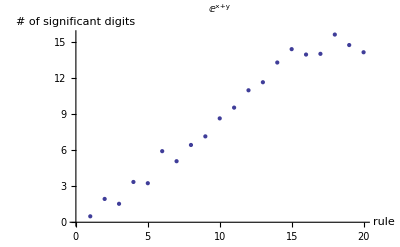

```mathematica
ClearAll[p,fun,a00,x,y,q,w]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=Exp[x+y];
Print["Mathematica value = ",a00=NIntegrate[fun[{x,y}],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20]];
Table[
{q,w}=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
-Log@Abs[(NIntegrateTriangleDunavantMethod[p,fun,{q,w}]-a00)/a00]/Log[10],
{rule,1,20}
]//ListPlot[#,AxesLabel->{"rule","# of significant digits"},AxesOrigin->{0,0},PlotLabel->fun[{x,y}]]&//Print;
```

Arcsinh method single triangle
	source triangle
	near-singular field point

Mathematica value=0.023963917173953-0.6902623825876617 ⅈ

best value=0.0239639-0.690262 ⅈ

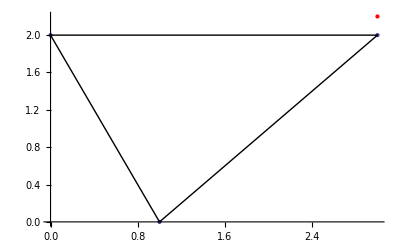

-Graphics3D-

```mathematica
ClearAll[P, P0,A, s1, s2, s3, wP, quadrules, iP]
P = {{1,0},{3,2},{0,2}} // N // ToPackedArray;
P0 = {3,2.2} // N // ToPackedArray;
A=Det[{P⟦2⟧-P⟦1⟧,P⟦3⟧-P⟦1⟧}];
s1 = A Det[{P[[1]] - P0, P[[2]] - P[[1]]}]>0;
s2 = A Det[{P[[2]] - P0, P[[3]] - P[[2]]}]>0;
s3 = A Det[{P[[3]] - P0, P[[1]] - P[[3]]}]>0;
wP = {1, 1, 1} // N // ToPackedArray;
If[!s1,wP⟦1⟧=-1.0];
If[!s2,wP⟦2⟧=-1.0];
If[!s3,wP⟦3⟧=-1.0];

ClearAll[fun, x, y, a0,a00]
fun[{x_, y_}] := Exp[ⅈ(x + 2y)];
raw = Table[
   quadrules = {LegendreRule[Nu, 0, 1], LegendreRule[Nv, 0, 1]};
   iP =
    {NIntegrateTriangleArcSinhMethod[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[3]], P[[1]]}, fun, quadrules]};
   a1 = iP.wP;
   {Nu, Nv, a1}
   ,
   {Nu, 30}, {Nv, 10}];
a00=NIntegrate[fun[{x,y}]/Norm[{x,y}-P0],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->16];
a0 = raw[[-1,-1, 3]];
Print["Mathematica value=",a00];
Print["best value=", a0];
data = {#[[1]], #[[2]], -Log@Abs[(#[[3]] - a0)/a0]/Log[10]} & /@ Flatten[raw, 1];
ListPlot[{P, {P0}}, PlotStyle -> {PointSize[Large], Red}, Epilog -> {Black, Line[P], Line[{P[[3]], P[[1]]}]}]
ListPlot3D[data, AxesLabel -> {"Nu", "Nv", "# of SD"}, PlotLabel -> fun[{x, y}],PlotRange->All,ImageSize -> Large]
```

Duffy - Only singular

In pt⟦np⟧: False

r={0.5,0.3}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.576214

best value for m=0 is: 0.013379

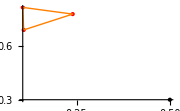
-Graphics-
-Graphics3D-

```mathematica
ClearAll[m,np,q,w,point,xx,data]
pStd={{0,0},{1,0},{0,1}};
m=0;
np=1;
point={0.5,0.3};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
data=Table[{q,w}=QuadratureProduct2D[LegendreRule[n2,0,1],LegendreRule[n1,0,1]];
xx=0.0;
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,1⟧,pt⟦np,2⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,2⟧,pt⟦np,3⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,3⟧,pt⟦np,1⟧},VscnmFuncR[m,point,#]&,{q,w}];
{n1,n2,xx},{n1,30},{n2,30}]//Flatten[#,1]&;
Print["best value for m=",m," is: ",data⟦-1,3⟧];
Print@TableForm@{
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small],
({#⟦1⟧,#⟦2⟧,-Log@Abs[#⟦3⟧-data⟦-1,3⟧]/Log[10]}&/@data)//ListPlot3D[#,PlotLabel->"DUFFY-SINGULAR "<>"m="<>ToString[m],AxesLabel->{"# of points","# of significant digits"},AxesOrigin->{0,0},ImageSize->Large]&};
```

Arcsinh method: Singular and near-singular and non-singular
Dunavant methods: Non-singular

In pt⟦np⟧: False

r={0.9,0.8}

cntr⟦np⟧={0.186399,0.306567}

|r-rp|≃0.867585

Rc = 0.0715497

best value for m= 40 is: 0.000176952+0.000298494 ⅈ

most # of SD by arcsinh = 6.46466 with 702 sampling points

most # of SD by Dunavant = 13.2249 with 79 sampling points

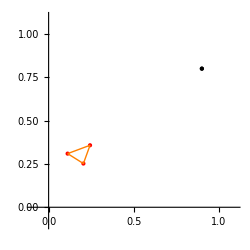
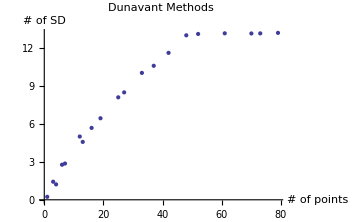
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
ClearAll[m,np,point,a0,a1]
m=40;
np=23;
point={0.9,0.8};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
Print["Rc = ",Rc⟦np⟧];
a0=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[100,0,1],LegendreRule[100,0,1]}];
raw1=Table[a1=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,a1},{Nu,1.2m+30},{Nv,3}]//Flatten[#,1]&;
data1={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw1;
raw2=Table[quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];{Length[quadrules⟦1⟧],NIntegrateTriangleDunavantMethod[pt⟦np⟧,VscnmFunc[m,point,#]&,quadrules]},{rule,1,20}];
data2={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw2;
Print["best value for m= ",m," is: ",a0];
Print["most # of SD by arcsinh = ",data1⟦-1,-1⟧," with ",3data1⟦-1,1⟧data1⟦-1,2⟧," sampling points"];
Print["most # of SD by Dunavant = ",data2⟦-1,-1⟧," with ",data2⟦-1,1⟧," sampling points"];
Print@{Show[
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->250,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AspectRatio->1]
],
ListPlot3D[data1,PlotRange->All,AxesLabel->{"Nu","Nv","# of SD"},PlotLabel->"ArcSinh Method",ImageSize->Medium],
ListPlot[data2,AxesLabel->{"# of points","# of SD"},PlotLabel->"Dunavant Methods",ImageSize->Medium]
}
```

Test the continuity of arcsinh method

```mathematica
ClearAll[quadrules,P,m,raw,xrange,yrange]
quadrules={LegendreRule[20,0,1],LegendreRule[4,0,1]};
P={{2,0},{3,2},{0,2}} // N // ToPackedArray;
m=0;
xrange=Range[0.001,3.0,0.03];
yrange=Range[-0.301,3.01,0.03];
raw=Table[{x,y,NIntegrateTriangleArcSinh2[{x,y},P,VscnmFuncR[m,{x,y},#]&,quadrules]},{y,yrange},{x,xrange}]//Flatten[#,1]&;
ListPlot3D[raw,InterpolationOrder->3,ImageSize->Large]
```

$Aborted

ListPlot3D::arrayerr: raw must be a valid array or a list of valid arrays.

ListPlot3D[raw,InterpolationOrder→3,ImageSize→Large]

12.3457

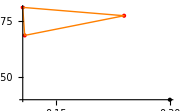

0.116115

```mathematica
ClearAll[n,m,ruleFar,ruleNear,mask,Mask,P,partialIntegral]
ruleFar=DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}];
ruleNear={LegendreRule[8,0,1],LegendreRule[3,0,1]};
Mask[P_]:=Table[Norm[P-cntr⟦n⟧]>0.2,{n,Ns}]
{n,m}={1,0};
P={0.3,0.4};
mask=Mask[P];
Total[If[#,0,1]&/@mask]/Ns*100//N
Print@ListPlot[{pt⟦n⟧,{P}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦n⟧],Line[{pt⟦n,1⟧,pt⟦n,3⟧}]},ImageSize->Small]
partialIntegral=Table[
If[mask⟦n⟧,
(*Far Field*)
NIntegrateTriangleDunavantMethod[pt⟦n⟧,VscnmFunc[m,P,#]&,ruleFar]
,
(*Near Field*)
NIntegrateTriangleArcSinh2[P,pt⟦n⟧,VscnmFuncR[m,P,#]&,ruleNear]
]
,{n,Ns}];
partialIntegral//Total//Print
```

```mathematica
ClearAll[n,m,QUADRULES,raw,time]
{n,m}={10,0};
QUADRULES={
{DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[8,0,1],LegendreRule[3,0,1]}},
{DunavantRule[10,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[10,0,1],LegendreRule[3,0,1]}},
{DunavantRule[15,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[12,0,1],LegendreRule[3,0,1]}},
{DunavantRule[20,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[15,0,1],LegendreRule[3,0,1]}}
};
Print["time = ",time=(raw=Table[NField[cntr⟦n⟧,m,QUADRULES⟦i⟧]*area⟦n⟧,{i,Length[QUADRULES]},{m,0,Nd}];)//AbsoluteTiming//#⟦1⟧&];
```

$Aborted

Non-singular Bnmnpmp

dr=0.804774

Rc=0.0700684

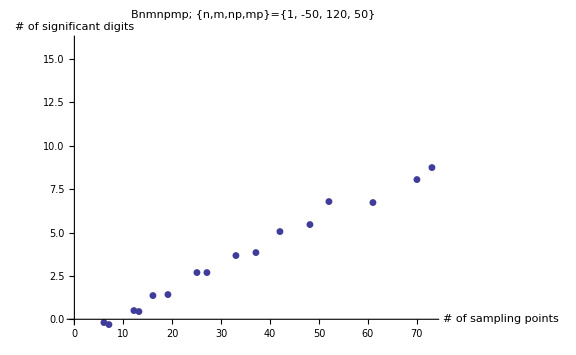

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules]
{n,m}={1,-50};
{np,mp}={120,50};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=False;
raw=Table[
quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
{quadrules⟦1⟧//Length,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{rule,20}
];
a0=raw⟦-1,2⟧;
data={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large,PlotMarkers->Automatic]
```

Singular Bnmnpmp

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules]
{n,m}={1,10};
{np,mp}={1,0};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=True;
raw=Table[
quadrules={LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]};
{Nu,Nv,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{Nu,100},{Nv,3}
]//Flatten[#,1]&;
a0=raw⟦-1,3⟧;
data={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot3D[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large]
```

dr=0.

Rc=0.0700684

-Graphics3D-

Non-singular SVD

dr=0.728111

Rc=0.0700684

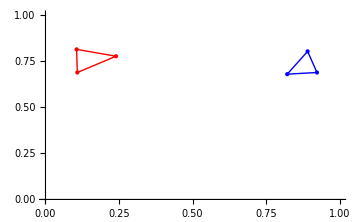

Dim/@{u,w,v}={{81,10},{10,10},{81,10}}

Max relative diff = 7.44206×10^-14

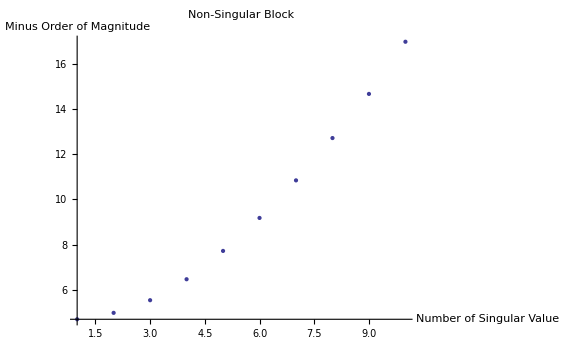

```mathematica
ClearAll[n,np,ArcSinhFlag,quadrules,raw]
{n,np}={1,10};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
Show[
ListPlot[pt⟦n⟧,ImageSize->Medium,PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,1},{0,1}},Epilog->{Red,Line[pt⟦n⟧],Line[{pt⟦n,3⟧,pt⟦n,1⟧}],Blue,Line[pt⟦np⟧],Line[{pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Blue,PointSize[Medium]}]
]
ArcSinhFlag=False;
quadrules=DunavantRule[12,{{0,0},{1,0},{0,1}}];
raw=ParallelTable[Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}];
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot;
ClearAll[rank,u,w,v]
rank=Length[SingularValueList[raw]];
{u,w,v}=SingularValueDecomposition[raw,rank];
Print["Dim/@{u,w,v}=",Dimensions/@{u,w,v}];
Print["Max relative diff = ",Norm/@Flatten[(u.w.v†-raw)/raw]//Max];
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot[#,PlotRange->All,AxesLabel->{"Number of Singular Value","Minus Order of Magnitude"},PlotLabel->"Non-Singular Block",ImageSize->Large]&
```

Singular block analysis - banded structure

dr=0.

Rc=0.0700684

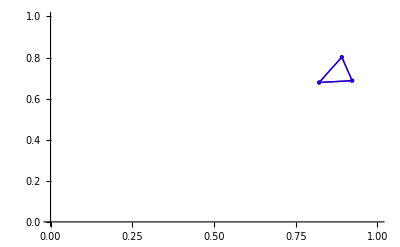

```mathematica
ClearAll[Nu,Nv,n,np,ArcSinhFlag,quadrules,raw]
{Nu,Nv}={100,3};
{n,np}={10,10};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
Show[
ListPlot[pt⟦n⟧,PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,1},{0,1}},Epilog->{Red,Line[pt⟦n⟧],Line[{pt⟦n,3⟧,pt⟦n,1⟧}],Blue,Line[pt⟦np⟧],Line[{pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Blue,PointSize[Medium]}]
]
ArcSinhFlag=True;
quadrules={LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]};
raw=ParallelTable[Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}];
```

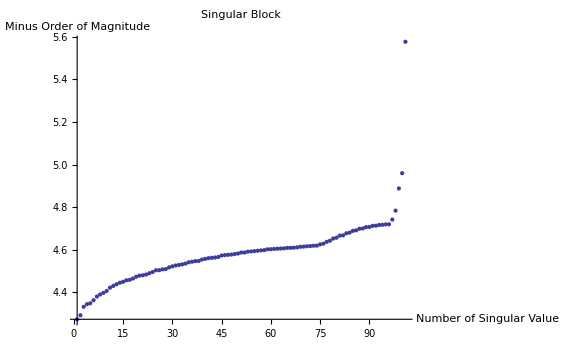

```mathematica
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot[#,PlotRange->All,AxesLabel->{"Number of Singular Value","Minus Order of Magnitude"},PlotLabel->"Singular Block",ImageSize->Large]&
```

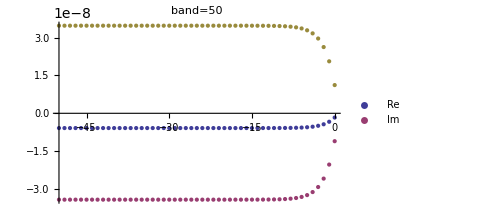
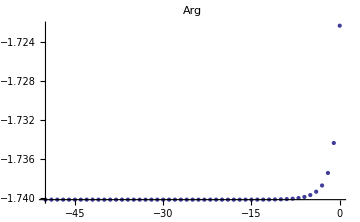

```mathematica
ClearAll[diagRe,diagIm,diagNorm,diagArg,band]
band=50;
diagRe=Table[{i-Nd-1,raw⟦i+band,i⟧//Re},{i,1,Nm-band}];
diagIm=Table[{i-Nd-1,raw⟦i+band,i⟧//Im},{i,1,Nm-band}];
diagNorm=Table[{i-Nd-1,raw⟦i+band,i⟧//Norm},{i,1,Nm-band}];
diagArg=Table[{i-Nd-1,raw⟦i+band,i⟧//Arg},{i,1,Nm-band}];
{
ListPlot[{diagRe,diagIm,diagNorm},PlotRange->All,PlotStyle->{{},{Thick,Dashed}},PlotLabel->"band="<>ToString[band],PlotLegends->{"Re","Im"},ImageSize->Medium],
diagArg//ListPlot[#,PlotRange->All,PlotLabel->"Arg",ImageSize->Medium]&
}
```

FittedModel[-5.85312×10^-9+6.94121×10^-9 ⅇ^(-0.510826 x)]

FittedModel[-5.85312×10^-9+6.94121×10^-9 ⅇ^(-0.510826 x)]

Max relative err=1.82842×10^-10

Max relative err=1.24223×10^-13

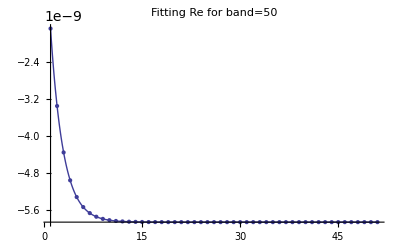

FittedModel[3.42237×10^-8-3.86154×10^-8 ⅇ^(-0.510826 x)]

FittedModel[-106.52+106.52 ⅇ^(-1. x)]

Max relative err=1.55386×10^-10

Max relative err=-3.11245×10^9

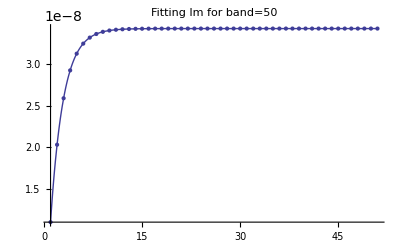

```mathematica
ClearAll[band,rawp,range,lm1,lm1p,lm2,lm2p,a,b,c,x]
range={1,2,3,4,Nd+1};
band=Nd;
rawp=Table[raw⟦i,i+band⟧//Re,{i,1,Nm-band}];
(lm1=NonlinearModelFit[rawp,a+c Exp[-b x],{a,b,c},x])//Print
(lm1p=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧}//Re,{i,range}],a+c Exp[-b x],{a,b,c},x])//Print
Max[Table[(lm1[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Max[Table[(lm1p[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Show[
ListPlot[rawp,PlotRange->All,PlotLabel->"Fitting Re for band=50"],
Plot[lm1p[x],{x,1,Nd+1},PlotRange->All]
]//Print
rawp=Table[raw⟦i,i+band⟧//Im,{i,1,Nm-band}];
(lm2=NonlinearModelFit[rawp,-a-c Exp[-b x],{a,b,c},x])//Print
(lm2p=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧}//Im,{i,range}],a+c Exp[-b x],{a,b,c},x])//Print
Max[Table[(lm2[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Max[Table[(lm2p[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Show[
ListPlot[rawp,PlotRange->All,PlotLabel->"Fitting Im for band=50"],
Plot[lm2[x],{x,1,Nd+1},PlotRange->All]
]//Print
```

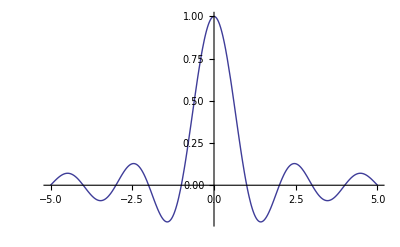

```mathematica
Plot[Sinc[π x],{x,-5,5},PlotRange->All]
```

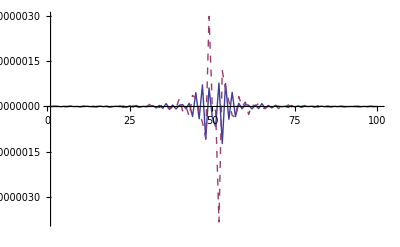

```mathematica
ClearAll[Δm,rawp2]
rawp2=Table[raw⟦i,Nm-i⟧,{i,1,Nm}];
ListLinePlot[{Re[rawp2],Im[rawp2]},PlotStyle->{{},{Dashed,Thick}},PlotRange->All]
```

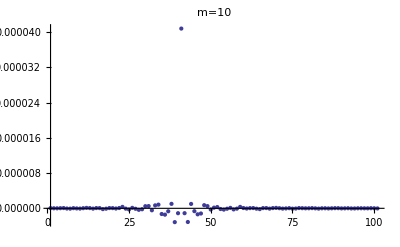

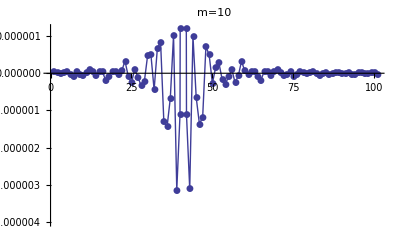

```mathematica
ClearAll[m]
m=10;
ListPlot[Re@raw⟦Nd+1-m⟧,PlotRange->All,PlotLabel->"m="<>ToString[m]]
ListLinePlot[Re@raw⟦Nd+1-m⟧,PlotRange->{-0.000004,0.0000012},PlotMarkers->Automatic,PlotLabel->"m="<>ToString[m]]
```

Cross approximation on non-singular blocks

```mathematica
ClearAll[MaxValueLocationC]
MaxValueLocationC=Compile[{{a,_Complex,2}},
Module[{i,j,i0,j0,m,n,max},{m,n}=Dimensions[a];{i0,j0}={1,1};max=Abs[a⟦1,1⟧];
For[i=1,i≤m,i++,For[j=1,j≤n,j++,If[Abs[a⟦i,j⟧]>max,{i0,j0}={i,j};max=Abs[a⟦i0,j0⟧];];];];
{i0,j0}]];
```

dr=0.804774

Rc=0.0700684

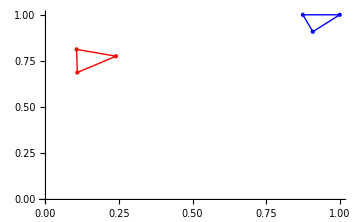

```mathematica
ClearAll[n, np, ArcSinhFlag, quadrules, raw]
{n, np} = {1, 120};
Print["dr=", Norm[cntr[[n]] - cntr[[np]]]];
Print["Rc=", Rc // Mean];
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
ArcSinhFlag = False;
quadrules = DunavantRule[20, {{0, 0}, {1, 0}, {0, 1}}];
raw = ParallelTable[Bnmnpmp[n, m, np, mp, ArcSinhFlag, quadrules], {m, -Nd, Nd}, {mp, -Nd, Nd}];
```

FittedModel[-3.3018×10^-7+2.07802×10^-7 ⅇ^(-0.510826 x)]

3.81764×10^-11

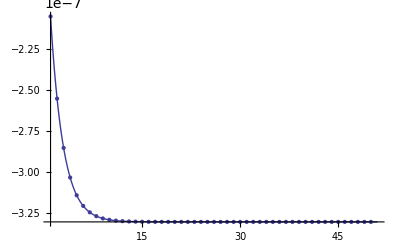

```mathematica
ClearAll[diagRe,band,a,b,c,x];
band=Nd+1;
diagRe=Table[raw⟦i,i+band⟧//Re,{i,1,Nm-band}];
(lm=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧//Re},{i,1,Nm-band}],a+b Exp[-c x],{a,b,c},x])//Print
Max[Table[Norm[(lm[i]-raw⟦i,i+band⟧//Re)/(raw⟦i,i+band⟧//Re)],{i,1,Nm-band}]]//Print
Show[
ListPlot[diagRe,PlotRange->All],
Plot[lm[x],{x,1,Nd+1},PlotRange->All]
]
```

Check accuracy: Norm[Z-∑_ν a bᵀ]/Norm[Z]=3.4095×10^-15

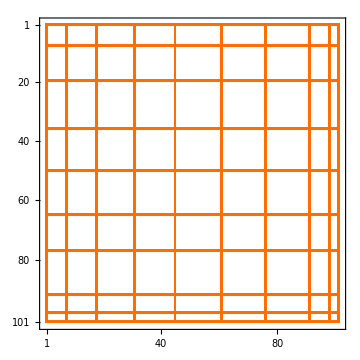

```mathematica
ClearAll[ν,i0,j0,A,B,R]
eps=1.0*10^-14;
R=raw;
A={};
B={};
ROW={};
COL={};
For[ν=1,ν≤10,ν++,
{i0,j0}=MaxValueLocationC[R];
If[(xx=Abs[R⟦i0,j0⟧]/Norm[raw,"Frobenius"])<eps,
Print["Terminate: rank=",ν-1,", eps=",xx];Break[];
];
AppendTo[ROW,i0];
AppendTo[COL,j0];
AppendTo[A,R⟦All,j0⟧];
AppendTo[B,R⟦i0⟧/R⟦i0,j0⟧];
R=R-Outer[Times,A⟦ν⟧,B⟦ν⟧];
];
Print["Check accuracy: Norm[Z-∑_ν a bᵀ]/Norm[Z]=",
Norm[raw-∑_(ν=1)^Length[A] Outer[Times,A⟦ν⟧,B⟦ν⟧]]/Norm[raw]];

ClearAll[PrintO]
PrintO[Nm_,row_,col_]:=Module[{n,r,A},
r=Length[row];A=ConstantArray[0,{Nm,Nm}];
For[n=1,n≤r,n++,
A⟦All,col⟦n⟧⟧=1;
A⟦row⟦n⟧,All⟧=1;
];
MatrixPlot[A]
]
PrintO[Nm,ROW,COL]//Print
```

```mathematica
ROW
COL
```

{1,61,31,48,12,56,5,22}

{1,61,26,46,10,55,17,37}

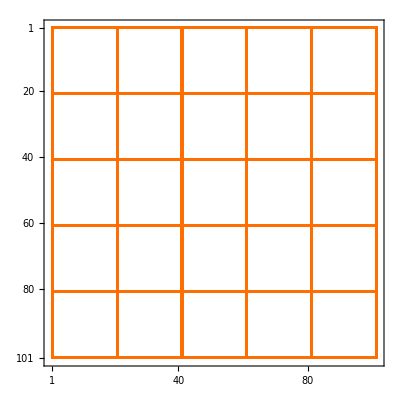

```mathematica
ROW=Range[1,Nm,20];
COL=ROW;
PrintO[Nm,ROW,COL]//Print
```

```mathematica
ClearAll[U,VT,S,eps,u,w,v]
U=raw⟦All,COL⟧;
VT=raw⟦ROW⟧;
S=Outer[raw⟦#1,#2⟧&,ROW,COL];
eps=10^-10;
{u,w,v}=SingularValueDecomposition[S,Length@SingularValueList[S,Tolerance->eps]];
Norm/@((S-u.w.vᵀ*)/S)//Max
Norm/@((U.(v.Inverse[w].uᵀ*).VT-raw)/raw)//Max
Length[w]
```

3.00512×10^-10

2.69937×10^-7

8

### Toeplitz Compression

DunavantMethod uses quadrature rules generated by
	DunavantRule[rule,{{0,0},{0,1},{1,0}}]
where
	rule is an integer between 1 and 20

ArcSinhMethod uses quadrature rules
	{LegendreRule[Nu,0,1],
	LegendreRule[Nv,0,1]}
where
	Nu and Nv are the number of sampling points in the u- and the v- directions

```mathematica
ClearAll[BtBandFunc,BtBandFuncR,BsBandFunc,BsBandFuncR,BtBandArcSinhMethod,BtBandDunavantMethod,BsBandArcSinhMethod,BsBandDunavantMethod]
BtBandFunc[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
mut[rp]Exp[-ⅈ Δm phir2rp]/Norm[dr]
]
BtBandFuncR[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
mut[rp]Exp[-ⅈ Δm phir2rp]
]
BsBandFunc[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
-mus[rp]Exp[-ⅈ Δm phir2rp]/Norm[dr]
]
BsBandFuncR[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
-mus[rp]Exp[-ⅈ Δm phir2rp]
]

BtBandDunavantMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BtBandFunc[Δm,cntr⟦n⟧,#]&,quadrules]
BtBandArcSinhMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BtBandFuncR[Δm,cntr⟦n⟧,#]&,quadrules]
BsBandDunavantMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BsBandFunc[Δm,cntr⟦n⟧,#]&,quadrules]
BsBandArcSinhMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BsBandFuncR[Δm,cntr⟦n⟧,#]&,quadrules]
```

Test elementwise correctness of the new matrix elements

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
raw=Bnmnpmp[n,m,np,mp,False,quadrules]
BtBandDunavantMethod[n,np,m-mp,quadrules]+BsBandDunavantMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

Part::partd: Part specification pt ⟦ 120 ⟧ is longer than depth of object.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::partd: Part specification cntr ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.5 Abs[Det[Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}]]] area⟦1⟧ area⟦120⟧ ((0.000704405 ⅇ^(16 ⅈ phir2rp$10307) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10312) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10247) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10283) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10288) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10319) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10324) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10275) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10276) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10295) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10300) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10250) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10313) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10318) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10272) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10273) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10277) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10282) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10269) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10270) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10322) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10320) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10301) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10306) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10253) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10266) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10267) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10289) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10294) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10316) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10314) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10310) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10308) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10263) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10264) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10256) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10304) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10302) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10298) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10296) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10260) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10261) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10292) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10290) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}+cntr⟦1⟧]+(0.0330571 ⅇ^(16 ⅈ phir2rp$10246) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10280) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10278) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10286) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10284) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10258) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10257) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10255) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10254) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10252) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10251) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10259) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10249) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10248) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10291) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10293) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10279) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10281) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10285) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10287) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10262) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10303) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10305) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10297) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10299) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10265) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10315) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10317) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10309) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10311) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10268) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10271) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10321) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10323) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10274) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}+cntr⟦1⟧])

Part::partd: Part specification area ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification area ⟦ 120 ⟧ is longer than depth of object.

Part::partd: Part specification pt ⟦ 120 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::pspec: Part specification 31 + Nd is neither a machine-sized integer nor a list of machine-sized integers.

0.5 Abs[Det[Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}]]] ((0.000704405 ⅇ^(«1») mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}])/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}+cntr⟦1⟧]+«80»+(«1»)/Norm[-pt-«1»+cntr⟦1⟧]) area⟦1⟧ area⟦120⟧+0.5 «4» gTbl⟦31+Nd⟧

Test the FFT - prepare

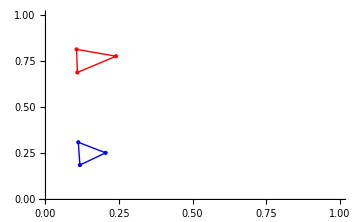

```mathematica
ClearAll[quadrules,n,np]
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
{n,np}={1,124};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,False,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

Test the FFT - y0=B.x0

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

Test the FFT - using FFT and compare results

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
ztf=Table[BtBandDunavantMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandDunavantMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandDunavantMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandDunavantMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=3.38434×10^-15

Do the same test of FFT on singular-blocks

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules={LegendreRule[15,0,1],LegendreRule[3,0,1]};
raw=Bnmnpmp[n,m,np,mp,True,quadrules]
BtBandArcSinhMethod[n,np,m-mp,quadrules]+BsBandArcSinhMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

-2.93362×10^-7-5.77309×10^-7 ⅈ

-2.93362×10^-7-5.77309×10^-7 ⅈ

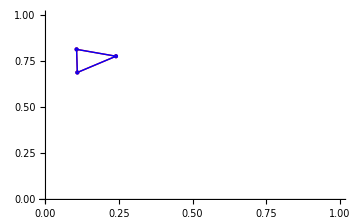

```mathematica
ClearAll[quadrules,n,np]
quadrules={LegendreRule[20,0,1],LegendreRule[3,0,1]};
{n,np}={1,1};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,True,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules={LegendreRule[20,0,1],LegendreRule[3,0,1]};
ztf=Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=3.89952×10^-15

Do the same test of FFT on near-singular-blocks

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules={LegendreRule[15,0,1],LegendreRule[3,0,1]};
raw=Bnmnpmp[n,m,np,mp,True,quadrules]
BtBandArcSinhMethod[n,np,m-mp,quadrules]+BsBandArcSinhMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

-2.93362×10^-7-5.77309×10^-7 ⅈ

-2.93362×10^-7-5.77309×10^-7 ⅈ

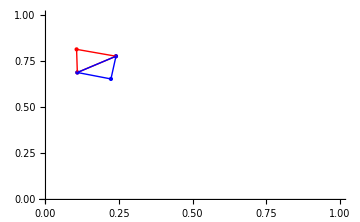

```mathematica
ClearAll[quadrules,n,np]
quadrules={LegendreRule[30,0,1],LegendreRule[3,0,1]};
{n,np}={1,2};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
```

```mathematica
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,True,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules={LegendreRule[30,0,1],LegendreRule[3,0,1]};
ztf=Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=9.04792×10^-15

## New Solver

First, compute the new input vector accurately using 1-point testing and multi-point source

```mathematica
ClearAll[VscnmFunc,VscnmFuncR]
VscnmFunc[m_,r_,rp_]:=Module[{dr,R,r2rphi},
dr=r-rp;R=Norm[dr];If[R<1.0*10^-13,r2rphi=0.0;,r2rphi=ArcTan[dr⟦1⟧,dr⟦2⟧];];
(*Exp[-ⅈ m r2rphi]/R*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m r2rphi]/R*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-rp⟦1⟧]
]
VscnmFuncR[m_,r_,rp_]:=Module[{dr,r2rphi},
dr=r-rp;If[Norm[dr]<1.0*10^-13,r2rphi=0.0;,r2rphi=ArcTan[dr⟦1⟧,dr⟦2⟧];];
(*Exp[-ⅈ m r2rphi]*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m r2rphi]*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-rp⟦1⟧]
]

ClearAll[NpField,VscnmNew]
NpField[P_,m_,QUADRULES_]:=Module[{n,ruleFar,ruleNear,mask,partialIntegral},
mask=Table[Norm[P-cntr⟦n⟧]>0.3,{n,Ns}];
partialIntegral=Table[
If[mask⟦i⟧,
(*Far Field*)NIntegrateTriangleDunavantMethod[pt⟦i⟧,VscnmFunc[m,P,#]&,QUADRULES⟦1⟧],
(*Near Field*)NIntegrateTriangleArcSinh2[P,pt⟦i⟧,VscnmFuncR[m,P,#]&,QUADRULES⟦2⟧]
]*area⟦i⟧
,{i,Ns}];
partialIntegral//Total
]

VscnmNew[n_,m_,QUADRULES_]:=area⟦n⟧NpField[cntr⟦n⟧,3,QUADRULES]
```

```mathematica
ClearAll[VscNEW,n,m,QUADRULES]
QUADRULES={DunavantRule[12,{{0,0},{0,1},{1,0}}],{LegendreRule[15,0,1],LegendreRule[3,0,1]}};
{n,m}={1,0};
(VscNEW=ParallelTable[VscnmNew[n,m,QUADRULES],{n,Ns},{m,-Nd,Nd}]//Flatten//ToCmplxPckdArry;)//AbsoluteTiming//#⟦1⟧&
```

1693.87549

```mathematica
SetDirectory[NotebookDirectory[]]
Export["VscNEW.re.dat",VscNEW//Re]
Export["VscNEW.im.dat",VscNEW//Im]
ResetDirectory[]
```

/Users/qzmfrank/Codes/rte2dvis/notebook

VscNEW.re.dat

VscNEW.im.dat

/Users/qzmfrank

```mathematica
VscnmNew[4,0,QUADRULES]
VscnmNew[4,2,QUADRULES]
```

0.0000109155+2.24672×10^-6 ⅈ

0.0000109155+2.24672×10^-6 ⅈ